```mathematica
SetOptions[Plot,BaseStyle->{FontFamily->"Helvetica",FontSize->14},TicksStyle->Directive[Black,10],Frame->True];
SetOptions[ListLinePlot,BaseStyle->{FontFamily->"Helvetica",FontSize->14},TicksStyle->Directive[Black,10],Frame->True];
SetOptions[ListPlot,BaseStyle->{FontFamily->"Helvetica",FontSize->14},PlotStyle->PointSize[0.02],TicksStyle->Directive[Black,10],Frame->True];
```

# Rydberg-Klein-Rees Potentials and PA lines for NaK

## Constants

```mathematica
a0=5.2917720859*10^-11;                   (*NIST site*)
h=6.62606896*10^-34;                   (*NIST site*)
ℏ=h/(2π);
hbar=1/(2π)h;
kB=1.3806504*10^-23;                   (*NIST site*)
me=9.10938215*10^-31;                   (*NIST site*)
mNa =3.81754066757446 10^-26;
mK41=6.80187059497004 10^-26;
mK40=6.63617749148248 10^-26;
mK39 = 6.47007514485677 10^-26;
u=1.660538782*10^-27;
Eh=4.35974394*10^-18;
c = 299792458;
cst = 1/(2π)h/(√(2 u))10^10 √(1/(100 c h));
muNa39K=(mNa*mK39)/(mNa+mK39)1/u
muNa40K=(mNa*mK40)/(mNa+mK40)1/u
muNa41K=(mNa*mK41)/(mNa+mK41)1/u
DeX = 5273.636 (*Potential minimum of the X1Σ ground state, according to Tiemann, with +0.015 increase to match a_triplet *)
df=10.0^-10
```

14.4587

14.5943

14.7252

5273.64

1.×10^-10

## Rydberg-Klein-Rees (RKR) Procedure

```mathematica
G=Compile[{np},Sum[Y[[i+1,1]] np^i,{i,0,9}],{{Y,_Real,2}}];
fd = Compile[{vp,np},Sqrt[G[np] - G[vp]]];
fm=Compile[{v},Sum[Y[[i+1,1+1]](v+0.5)^i,{i,0,7}],{{Y,_Real,2}}];
qv=Compile[{nd},2 Sqrt[df/Sum[i Y[[i+1,1]] nd^(i-1),{i,1,9}]],{{Y,_Real,2}}];
f = Compile[{n},NIntegrate[1/fd[v+0.5,n+0.5],{v,-0.5,n-df}]+qv[n+0.5]];
g=Compile[{n},NIntegrate[fm[v]/fd[v+0.5,n+0.5],{v,-0.5,n-df}]+fm[n]qv[n+0.5]];
s=Compile[{n},Sqrt[1+(1/(f[n]g[n]))]];
a=Compile[{n},(cst/Sqrt[mu])f[n](s[n]-1)];  (*inner turning point*)
b=Compile[{n},(cst/Sqrt[mu])f[n](s[n]+1)];  (*outer turning point*)
e=Compile[{v},G[v+0.5]];  (* energy of vibrational level*)
Term=Compile[{{Y,_Real,2},v,J},If[J==0,Sum[Y[[k+1,1]](v+0.5)^k,{k,0,9}],Sum[Sum[Y[[k+1,l+1]](v+0.5)^k,{k,0,9}](J(J+1))^l,{l,0,2}]]];
```

## B1Π state for Na^39 K Kasahara, Baba, Kato, J. Chem. Phys. 94, 7713 (1991) http://dx.doi.org/10.1063/1.460157

```mathematica
mu = muNa39K;
TeB1Pi = 16992.7446;
vmaxB1Pi = 43;
Y=Table[0,{i,1,10},{j,1,3}];  (*Dunham coefficients from the paper*)
Y[[All,All]]=0;
Y[[0+1,0+1]]=-0.0430;
Y[[1+1,0+1]]=71.4630;
Y[[2+1,0+1]]=-1.15092;
Y[[3+1,0+1]]=-1.0613 10^-2;
Y[[4+1,0+1]]=9.9950 10^-4;
Y[[5+1,0+1]]=-1.42656 10^-5;
Y[[6+1,0+1]]=-8.67783 10^-7;
Y[[7+1,0+1]]=4.74996 10^-8;
Y[[8+1,0+1]]=-9.30786 10^-10;
Y[[9+1,0+1]]=6.67343 10^-12;
Y[[0+1,1+1]]=7.23853 10^-2;
Y[[1+1,1+1]]=-1.17799 10^-3;
Y[[2+1,1+1]]=-1.3502 10^-5;
Y[[3+1,1+1]]=-4.7933 10^-7;
Y[[4+1,1+1]]=4.82977 10^-8;
Y[[5+1,1+1]]=-6.88606 10^-10;
Y[[6+1,1+1]]=-1.13984 10^-11;
Y[[7+1,1+1]]=2.09534 10^-13;
Y[[0+1,2+1]]=-2.89859 10^-7;
Y[[1+1,2+1]]=-1.93901 10^-8;
Y[[2+1,2+1]]=6.45399 10^-10;
Y[[3+1,2+1]]=-7.75355 10^-12;
Y[[4+1,2+1]]=9.91847 10^-13;
Y[[5+1,2+1]]=-3.46351 10^-14;
Y//MatrixForm
```

(-0.043 | 0.0723853 | -2.89859×10^-7
71.463 | -0.00117799 | -1.93901×10^-8
-1.15092 | -0.000013502 | 6.45399×10^-10
-0.010613 | -4.7933×10^-7 | -7.75355×10^-12
0.0009995 | 4.82977×10^-8 | 9.91847×10^-13
-0.0000142656 | -6.88606×10^-10 | -3.46351×10^-14
-8.67783×10^-7 | -1.13984×10^-11 | 0
4.74996×10^-8 | 2.09534×10^-13 | 0
-9.30786×10^-10 | 0 | 0
6.67343×10^-12 | 0 | 0)

## RKR Potential for B1Π:

CompiledFunction::cfsa: Argument 0.5`  + v at position 1 should be a machine-size real number.

General::stop: Further output of CompiledFunction will be suppressed during this calculation.

(0 | 35.3995 | 3.84659 | 4.21033
1 | 104.531 | 3.74007 | 4.37903
2 | 171.293 | 3.67338 | 4.51049
3 | 235.665 | 3.62286 | 4.62857
4 | 297.645 | 3.58172 | 4.74021
5 | 357.248 | 3.54691 | 4.84862
6 | 414.499 | 3.51677 | 4.9556
7 | 469.437 | 3.49026 | 5.06231
8 | 522.106 | 3.46671 | 5.16955
9 | 572.559 | 3.44561 | 5.2779
10 | 620.85 | 3.42662 | 5.38782
11 | 667.038 | 3.40945 | 5.49967
12 | 711.183 | 3.39388 | 5.61378
13 | 753.343 | 3.37973 | 5.73041
14 | 793.58 | 3.36682 | 5.84983
15 | 831.951 | 3.35503 | 5.97228
16 | 868.516 | 3.34422 | 6.09801
17 | 903.329 | 3.33431 | 6.22726
18 | 936.448 | 3.32519 | 6.36028
19 | 967.925 | 3.31678 | 6.49736
20 | 997.814 | 3.30901 | 6.63877
21 | 1026.17 | 3.30184 | 6.78486
22 | 1053.03 | 3.29522 | 6.93597
23 | 1078.45 | 3.28913 | 7.09255
24 | 1102.48 | 3.28354 | 7.25509
25 | 1125.15 | 3.27845 | 7.4242
26 | 1146.5 | 3.27387 | 7.60062
27 | 1166.57 | 3.26981 | 7.78529
28 | 1185.38 | 3.26626 | 7.97941
29 | 1202.95 | 3.26325 | 8.18448
30 | 1219.3 | 3.26077 | 8.40249
31 | 1234.42 | 3.25879 | 8.63601
32 | 1248.33 | 3.2573 | 8.8884
33 | 1261.01 | 3.25623 | 9.16413
34 | 1272.45 | 3.25551 | 9.46915
35 | 1282.64 | 3.25501 | 9.81146
36 | 1291.56 | 3.25461 | 10.202
37 | 1299.21 | 3.2542 | 10.6558
38 | 1305.62 | 3.25373 | 11.1936
39 | 1310.82 | 3.25347 | 11.8436
40 | 1314.9 | 3.25448 | 12.6402
41 | 1318.02 | 3.26006 | 13.6101
42 | 1320.41 | 3.27858 | 14.712
43 | 1322.43 | 3.32532 | 15.7067)

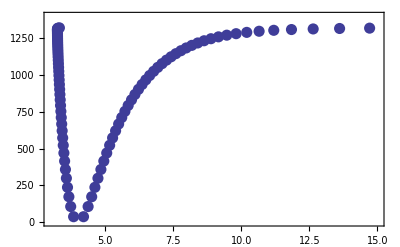

```mathematica
YB1PiNa39K = Y; (*The above defined Dunham coefficients are used here to recreate the RKR potential*)
mu = muNa39K;
RKRPotB1PiNa39K = Table[{v,e[v],a[v],b[v]},{v,0,43}]; (* RKR potential *)
BoundstatesB1PiNa39K = Table[{v,e[v]},{v,0,43}]; (* vibrational level, energy , inner and outer turning point *)
RKRPotB1PiNa39K//MatrixForm
ShowB1PiPot=Show[ListPlot[Table[{RKRPotB1PiNa39K[[v,3]],RKRPotB1PiNa39K[[v,2]]},{v,1,44}]],ListPlot[Table[{RKRPotB1PiNa39K[[v,4]],RKRPotB1PiNa39K[[v,2]]},{v,1,44}]], PlotRange->{{3,15},{0,1400}}] (* Energy versus inner- and outer turning points *)
```

### Fixing the issue of backbending of the RKR potential:

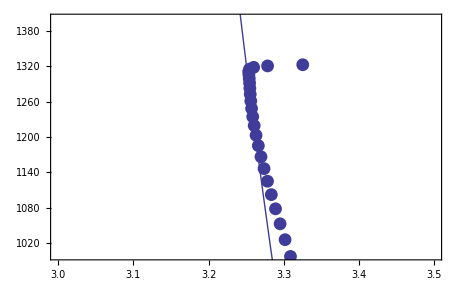

```mathematica
Vcorr[x_]:=3.85547 10^9/x^12-1450.79;(* Fitted form of potential from Kato *)
Show[ListPlot[Table[{RKRPotB1PiNa39K[[v,3]],RKRPotB1PiNa39K[[v,2]]},{v,1,44}]],ListPlot[Table[{RKRPotB1PiNa39K[[v,4]],RKRPotB1PiNa39K[[v,2]]},{v,1,44}]],Plot[Vcorr[x],{x,3.2,3.6}],PlotRange->{{3,3.5},{1000,1400}}]
```

(0 | 35.3995 | 3.84659 | 4.21033
1 | 104.531 | 3.74007 | 4.37903
2 | 171.293 | 3.67338 | 4.51049
3 | 235.665 | 3.62286 | 4.62857
4 | 297.645 | 3.58172 | 4.74021
5 | 357.248 | 3.54691 | 4.84862
6 | 414.499 | 3.51677 | 4.9556
7 | 469.437 | 3.49026 | 5.06231
8 | 522.106 | 3.46671 | 5.16955
9 | 572.559 | 3.44561 | 5.2779
10 | 620.85 | 3.42662 | 5.38782
11 | 667.038 | 3.40945 | 5.49967
12 | 711.183 | 3.39388 | 5.61378
13 | 753.343 | 3.37973 | 5.73041
14 | 793.58 | 3.36682 | 5.84983
15 | 831.951 | 3.35503 | 5.97228
16 | 868.516 | 3.34422 | 6.09801
17 | 903.329 | 3.33431 | 6.22726
18 | 936.448 | 3.32519 | 6.36028
19 | 967.925 | 3.31678 | 6.49736
20 | 997.814 | 3.30901 | 6.63877
21 | 1026.17 | 3.30184 | 6.78486
22 | 1053.03 | 3.29522 | 6.93597
23 | 1078.45 | 3.28913 | 7.09255
24 | 1102.48 | 3.28354 | 7.25509
25 | 1125.15 | 3.27845 | 7.4242
26 | 1146.5 | 3.27387 | 7.60062
27 | 1166.57 | 3.26981 | 7.78529
28 | 1185.38 | 3.26626 | 7.97941
29 | 1202.95 | 3.26325 | 8.18448
30 | 1219.3 | 3.26077 | 8.40249
31 | 1234.42 | 3.25879 | 8.63601
32 | 1248.33 | 3.2573 | 8.8884
33 | 1261.01 | 3.25623 | 9.16413
34 | 1272.45 | 3.25551 | 9.46915
35 | 1282.64 | 3.25422 | 9.81068
36 | 1291.56 | 3.25334 | 10.2007
37 | 1299.21 | 3.25259 | 10.6542
38 | 1305.62 | 3.25195 | 11.1918
39 | 1310.82 | 3.25144 | 11.8416
40 | 1314.9 | 3.25104 | 12.6368
41 | 1318.02 | 3.25074 | 13.6008
42 | 1320.41 | 3.2505 | 14.684
43 | 1322.43 | 3.25031 | 15.6317)

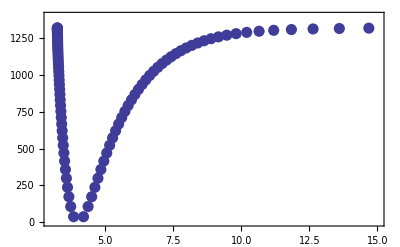

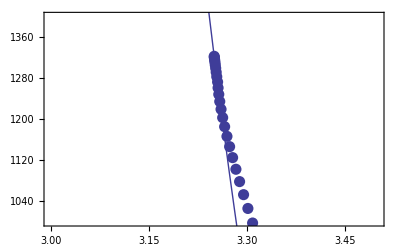

```mathematica
(* For the weakly bound states a unusual bending of the RKR potential is observed. This is simply corrected for here by using a fitted corrected potential (from Kato) and replacing the turning points from v=35 upwards to by that corrected potential... *)
RKRPotB1PiNaK39corr =RKRPotB1PiNa39K;
For[i=35,i<44,i+=1;
RKRPotB1PiNaK39corr[[i,3]]=x/.FindRoot[Vcorr[x]==RKRPotB1PiNa39K[[i,2]],{x,3}];
RKRPotB1PiNaK39corr[[i,4]]=RKRPotB1PiNa39K[[i,4]]-RKRPotB1PiNa39K[[i,3]]+x/.FindRoot[Vcorr[x]==RKRPotB1PiNa39K[[i,2]],{x,3}]
]
RKRPotB1PiNaK39corr//MatrixForm
ShowB1PiPot =Show[ListPlot[Table[{RKRPotB1PiNaK39corr[[v,3]],RKRPotB1PiNaK39corr[[v,2]]},{v,1,44}]],ListPlot[Table[{RKRPotB1PiNaK39corr[[v,4]],RKRPotB1PiNaK39corr[[v,2]]},{v,1,44}]], PlotRange->{{3,15},{0,1400}}]
Show[ListPlot[Table[{RKRPotB1PiNaK39corr[[v,3]],RKRPotB1PiNaK39corr[[v,2]]},{v,1,44}]],ListPlot[Table[{RKRPotB1PiNaK39corr[[v,4]],RKRPotB1PiNaK39corr[[v,2]]},{v,1,44}]],Plot[Vcorr[x],{x,3.2,3.6}],PlotRange->{{3,3.5},{1000,1400}}] (*This shows: There is no backbending anymore... *)
```

## Finding energies of Na^40 K and Na^41 K B1Π via mass scaling of Dunham coefficients: Dunham, Phys. Rev. 41, 721 (1932) http://prola.aps.org/abstract/PR/v41/i6/p721_1

```mathematica
(* This describes the mass scaling (and even corrections to simple mass scaling) to obtain the Dunham coefficients for 40K and 41K from those of 39Kd *)
```

#### Correction terms to simple mass scaling (essentially negligible for us...)

```mathematica
Y = YB1PiNa39K;
bc = Y;
bc[[All,All]]=0;
a1 = Y[[1+1,1+1]] Y[[1+1,0+1]]/(6 Y[[0+1,1+1]]^2)-1;
bc[[0+1,1+1]] = Y[[1+1,0+1]]^2 Y[[2+1,1+1]]/(4 Y[[0+1,1+1]]^3)+16 a1 Y[[2+1,0+1]]/(3Y[[0+1,1+1]])-8a1 - 6 a1^2+4 a1^3;
bc[[1+1,0+1]] = 5Y[[1+1,0+1]] Y[[3+1,0+1]]/(4 Y[[0+1,1+1]]^2)+a1 Y[[1+1,0+1]]^2 Y[[2+1,1+1]]/(3 Y[[0+1,1+1]]^3)-10 a1 -20 a1^2-15 a1^3/2-5 a1^4/2+Y[[2+1,0+1]](4 a1 + 16 a1^2/3)/Y[[0+1,1+1]]+Y[[2+1,0+1]]^2/(2 Y[[0+1,1+1]]^2);
bc[[0+1,2+1]] = 73/2+37a1 + 67 a1^2/2+33 a1^3-6 a1^4-9Y[[1+1,0+1]] Y[[3+1,0+1]]/(2 Y[[0+1,1+1]]^2)+Y[[1+1,0+1]]^2 Y[[2+1,1+1]](3-11a1/6)/(2 Y[[0+1,1+1]]^3)-Y[[2+1,0+1]](130/3+4a1+74 a1^2/3)/(2Y[[0+1,1+1]])+31 Y[[2+1,0+1]]^2/(9 Y[[0+1,1+1]]^2);
typicalcorrection = bc[[0+1,1+1]](YB1PiNa39K[[0+1,1+1]]/YB1PiNa39K[[1+1,0+1]])^2(muNa39K-muNa40K)/muNa40K
```

-1.49683×10^-7

### Do mass scaling for Na40K

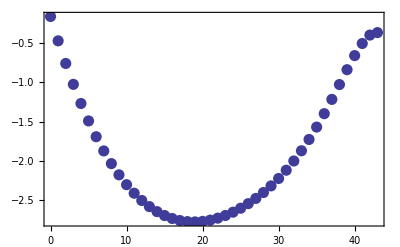

```mathematica
(*Here the mass scaled Dunham coefficients are calculated. The "simple" mass scaling term is the (muNa39K/muNa40)^[(i+2j)/2] factor*)

YB1PiNa40K = YB1PiNa39K;
For[i=1,i<10,i++,
For[j=0,j<3,j++,
YB1PiNa40K[[i+1,j+1]]=YB1PiNa39K[[i+1,j+1]](muNa39K/muNa40K)^((i+2j)/2)(1+bc[[i+1,j+1]](YB1PiNa39K[[0+1,1+1]]/YB1PiNa39K[[1+1,0+1]])^2(muNa39K-muNa40K)/muNa40K)
]]
Y=YB1PiNa40K;
mu = muNa40K;
BoundstatesB1PiNa40K = Table[{v,e[v]},{v,0,43}];
IsotopeshiftB1Pi = Table[{v,BoundstatesB1PiNa40K[[v+1,2]]-BoundstatesB1PiNa39K[[v+1,2]]},{v,0,43}];
PAlinesB1PiNa40K =Table[{v,TeB1Pi - YB1PiNa40K[[1,1]]- DeX+BoundstatesB1PiNa40K[[v+1,2]]},{v,0,43}];
PAwavelengthB1PiNa40K = Table[{v,1/100/PAlinesB1PiNa40K[[v+1,2]] 10^9},{v,0,43}];
ListPlot[IsotopeshiftB1Pi] (*Plotting the isotope shift from the PA lines... on the order of one wavenumber.*)
```

CompiledFunction::cfsa: Argument 0.5`  + v at position 1 should be a machine-size real number.

General::stop: Further output of CompiledFunction will be suppressed during this calculation.

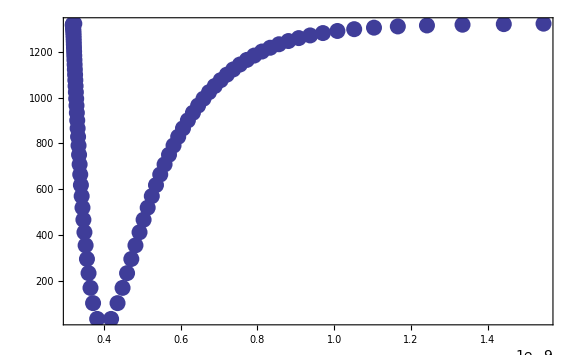

```mathematica
B1PiNa40Kpot=Table[{v,e[v],a[v],b[v]},{v,0,43}];
InnerTurningPoint=Table[{B1PiNa40Kpot[[i,3]] 10^-10 ,B1PiNa40Kpot[[i,2]]},{i,1,44}]; 
OuterTurningPoint=Table[{B1PiNa40Kpot[[i,4]] 10^-10 ,B1PiNa40Kpot[[i,2]]},{i,1,44}];
B1PiNa40KpotR=Sort[Flatten[Join[{InnerTurningPoint,OuterTurningPoint}],1]];
ListPlot[B1PiNa40KpotR]
```

### Do mass scaling for Na41K

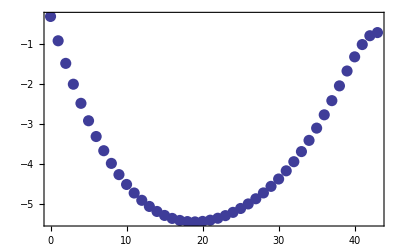

```mathematica
YB1PiNa41K = YB1PiNa39K;
For[i=1,i<10,i++,
For[j=0,j<3,j++,
YB1PiNa41K[[i+1,j+1]]=YB1PiNa39K[[i+1,j+1]](muNa39K/muNa41K)^((i+2j)/2)(1+bc[[i+1,j+1]](YB1PiNa39K[[0+1,1+1]]/YB1PiNa39K[[1+1,0+1]])^2(muNa39K-muNa41K)/muNa41K)
]]
Y=YB1PiNa41K;
mu = muNa41K;
BoundstatesB1PiNa41K = Table[{v,e[v]},{v,0,43}];
IsotopeshiftB1Pi39K41K = Table[{v,BoundstatesB1PiNa41K[[v+1,2]]-BoundstatesB1PiNa39K[[v+1,2]]},{v,0,43}];
PAlinesB1PiNa41K =Table[{v,TeB1Pi - YB1PiNa40K[[1,1]]- DeX+BoundstatesB1PiNa41K[[v+1,2]]},{v,0,43}];
PAwavelengthB1PiNa41K = Table[{v,1/100/PAlinesB1PiNa41K[[v+1,2]] 10^9},{v,0,43}];
ListPlot[IsotopeshiftB1Pi39K41K](*Plotting the isotope shift from the PA lines... on the order of few wavenumbers.*)
```

## c3Σ+ state for Na^39 K R. Ferber et al., J. Chem. Phys. 112, 5740 (2000) http://dx.doi.org/10.1063/1.481149

```mathematica
(* Now: Same game as above for the c-triplet-sigma-plus potential... Dunham coefficients from Kato...*)
```

```mathematica
mu = muNa39K;
Tec3sigmaplus = 15750.64;
vmaxc3SigmaPlus =50;
Y=Table[0,{i,1,10},{j,1,3}];
Y[[All,All]]=0;
Y[[0+1,0+1]]=0;
Y[[1+1,0+1]]=73.4;
Y[[2+1,0+1]]=-0.480173;
Y[[3+1,0+1]]=-9.82485 10^-4;
Y[[0+1,1+1]]=0.06275;
Y[[1+1,1+1]]=-5.91425 10^-4;
Y[[2+1,1+1]]=-1.81058 10^-6;
Y[[0+1,2+1]]=1.83 10^-7;
Y[[1+1,2+1]]=3.45 10^-9;
Y[[2+1,2+1]]=-2.17 10^-11;
Y//MatrixForm
```

(0 | 0.06275 | 1.83×10^-7
73.4 | -0.000591425 | 3.45×10^-9
-0.480173 | -1.81058×10^-6 | -2.17×10^-11
-0.000982485 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)

## RKR Potential for c3Σ+:

CompiledFunction::cfsa: Argument 0.5`  + v at position 1 should be a machine-size real number.

General::stop: Further output of CompiledFunction will be suppressed during this calculation.

(0 | 36.5798 | 4.14226 | 4.49971
1 | 109.016 | 4.03093 | 4.6535
2 | 180.484 | 3.95962 | 4.7679
3 | 250.976 | 3.9047 | 4.86657
4 | 320.487 | 3.85933 | 4.95638
5 | 389.011 | 3.82039 | 5.04046
6 | 456.543 | 3.78616 | 5.12056
7 | 523.076 | 3.75556 | 5.19779
8 | 588.604 | 3.72785 | 5.2729
9 | 653.122 | 3.70253 | 5.34642
10 | 716.624 | 3.67922 | 5.41876
11 | 779.103 | 3.65763 | 5.49025
12 | 840.554 | 3.63752 | 5.56114
13 | 900.971 | 3.61871 | 5.63165
14 | 960.348 | 3.60105 | 5.70197
15 | 1018.68 | 3.58443 | 5.77225
16 | 1075.96 | 3.56872 | 5.84264
17 | 1132.18 | 3.55384 | 5.91328
18 | 1187.34 | 3.53972 | 5.98427
19 | 1241.43 | 3.52628 | 6.05575
20 | 1294.44 | 3.51347 | 6.1278
21 | 1346.38 | 3.50123 | 6.20055
22 | 1397.22 | 3.48951 | 6.2741
23 | 1446.97 | 3.47827 | 6.34854
24 | 1495.63 | 3.46747 | 6.42399
25 | 1543.18 | 3.45708 | 6.50055
26 | 1589.61 | 3.44705 | 6.57832
27 | 1634.94 | 3.43735 | 6.65743
28 | 1679.14 | 3.42796 | 6.73799
29 | 1722.21 | 3.41884 | 6.82012
30 | 1764.14 | 3.40997 | 6.90396
31 | 1804.94 | 3.40131 | 6.98964
32 | 1844.59 | 3.39284 | 7.07732
33 | 1883.09 | 3.38452 | 7.16716
34 | 1920.43 | 3.37634 | 7.25932
35 | 1956.61 | 3.36825 | 7.35401
36 | 1991.61 | 3.36023 | 7.45143
37 | 2025.45 | 3.35224 | 7.55182
38 | 2058.1 | 3.34425 | 7.65542
39 | 2089.56 | 3.33622 | 7.76253
40 | 2119.83 | 3.32811 | 7.87345
41 | 2148.9 | 3.31987 | 7.98855
42 | 2176.77 | 3.31146 | 8.10822
43 | 2203.42 | 3.30282 | 8.23295
44 | 2228.86 | 3.29389 | 8.36324
45 | 2253.08 | 3.28459 | 8.49971
46 | 2276.06 | 3.27485 | 8.64309
47 | 2297.81 | 3.26457 | 8.7942
48 | 2318.33 | 3.25363 | 8.95404
49 | 2337.59 | 3.24191 | 9.12381
50 | 2355.61 | 3.22924 | 9.30496)

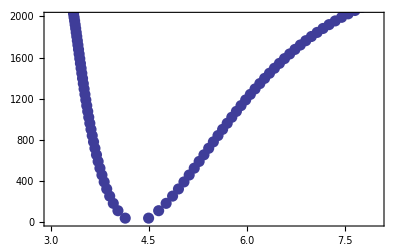

```mathematica
(* with the RKR routine that directly gives the energy versus inner/outer turning points*)
Yc3SigmaPlusNa39K = Y;
RKRPotc3SigmaPlusNa39K = Table[{v,e[v],a[v],b[v]},{v,0,50}];
Boundstatesc3SigmaPlusNa39K = Table[{v,e[v]},{v,0,50}];
RKRPotc3SigmaPlusNa39K//MatrixForm
Showc3SigmaPlusPot =Show[ListPlot[Table[{RKRPotc3SigmaPlusNa39K[[v,3]],RKRPotc3SigmaPlusNa39K[[v,2]]},{v,1,51}]],ListPlot[Table[{RKRPotc3SigmaPlusNa39K[[v,4]],RKRPotc3SigmaPlusNa39K[[v,2]]},{v,1,51}]], PlotRange->{{3,8},{0,2000}}]
```

### RKR From Ferber et al.:

```mathematica
(*this benchmarks our RKR versus the RKR potentials obtained by Ferber et al.*)
```

```mathematica
RKRPotc3SigmaPlusNa39KFerber={{0,36.59,4.1422,4.4997},{1,109.02,4.0309,4.6535},{2,180.49,3.9596,4.7679},{3,250.98,3.9047,4.8666},{4,320.49,3.8593,4.9564},{5,389.02,3.8204,5.0405},{6,456.55,3.7862,5.1206},{7,523.08,3.7556,5.1978},{8,588.61,3.7279,5.2729},{9,653.13,3.7025,5.3464},{10,716.63,3.6792,5.4188},{11,779.11,3.6576,5.4903},{12,840.56,3.6375,5.5611},{13,900.98,3.6187,5.6317},{14,960.35,3.6011,5.702},{15,1018.69,3.5844,5.7723},{16,1075.97,3.5687,5.8427},{17,1132.19,3.5538,5.9133},{18,1187.35,3.5397,5.9843},{19,1241.44,3.5263,6.0558},{20,1294.45,3.5135,6.1278},{21,1346.38,3.5012,6.2006},{22,1397.23,3.4895,6.2741},{23,1446.98,3.4783,6.3485},{24,1495.63,3.4675,6.424},{25,1543.18,3.4571,6.5006},{26,1589.62,3.4471,6.5783},{27,1634.94,3.4374,6.6574},{28,1679.14,3.428,6.738},{29,1722.21,3.4188,6.8201},{30,1764.15,3.41,6.904},{31,1804.95,3.4013,6.9897},{32,1844.6,3.3928,7.0773},{33,1883.09,3.3845,7.1672},{34,1920.44,3.3763,7.2593},{35,1956.61,3.3683,7.354},{36,1991.62,3.3602,7.4514}};
```

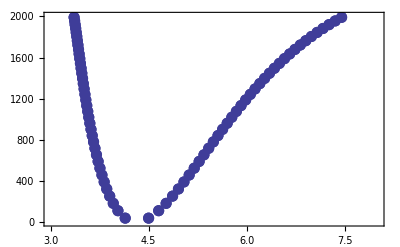

```mathematica
Show[ListPlot[Table[{RKRPotc3SigmaPlusNa39K[[v,3]],RKRPotc3SigmaPlusNa39K[[v,2]]},{v,1,37}]],ListPlot[Table[{RKRPotc3SigmaPlusNa39K[[v,4]],RKRPotc3SigmaPlusNa39K[[v,2]]},{v,1,37}]],
ListPlot[Table[{RKRPotc3SigmaPlusNa39KFerber[[v,3]],RKRPotc3SigmaPlusNa39KFerber[[v,2]]},{v,1,37}]],ListPlot[Table[{RKRPotc3SigmaPlusNa39KFerber[[v,4]],RKRPotc3SigmaPlusNa39KFerber[[v,2]]},{v,1,37}]], PlotRange->{{3,8},{0,2000}}]
```

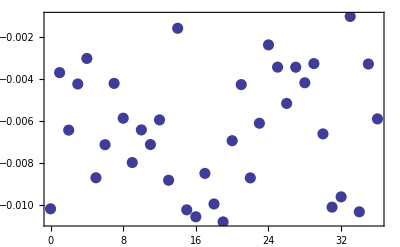

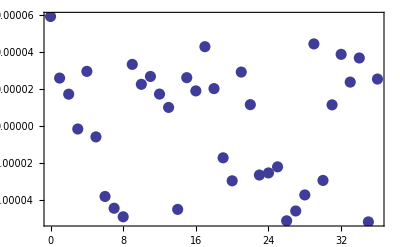

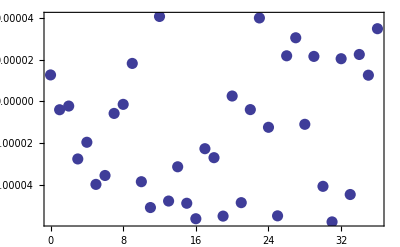

```mathematica
ListPlot[Table[{RKRPotc3SigmaPlusNa39K[[v,1]],RKRPotc3SigmaPlusNa39K[[v,2]]-RKRPotc3SigmaPlusNa39KFerber[[v,2]]},{v,1,37}]]
ListPlot[Table[{RKRPotc3SigmaPlusNa39K[[v,1]],RKRPotc3SigmaPlusNa39K[[v,3]]-RKRPotc3SigmaPlusNa39KFerber[[v,3]]},{v,1,37}]]
ListPlot[Table[{RKRPotc3SigmaPlusNa39K[[v,1]],RKRPotc3SigmaPlusNa39K[[v,4]]-RKRPotc3SigmaPlusNa39KFerber[[v,4]]},{v,1,37}]]
```

```mathematica
(*Everything seems fine with our RKR potential: Energy is somehow systematically on the low side, but only by 10^-7. Inner and outer turning points fluctuate pretty randomly...*)
```

## Finding energies of Na^40 K and Na^41 K c3Σ+ via mass scaling of Dunham coefficients: Dunham, Phys. Rev. 41, 721 (1932) http://prola.aps.org/abstract/PR/v41/i6/p721_1

#### Correction terms to simple mass scaling (essentially negligible for us...)

```mathematica
Y = Yc3SigmaPlusNa39K;
bc = Y;
bc[[All,All]]=0;
a1 = Y[[1+1,1+1]] Y[[1+1,0+1]]/(6 Y[[0+1,1+1]]^2)-1;
bc[[0+1,1+1]] = Y[[1+1,0+1]]^2 Y[[2+1,1+1]]/(4 Y[[0+1,1+1]]^3)+16 a1 Y[[2+1,0+1]]/(3Y[[0+1,1+1]])-8a1 - 6 a1^2+4 a1^3;
bc[[1+1,0+1]] = 5Y[[1+1,0+1]] Y[[3+1,0+1]]/(4 Y[[0+1,1+1]]^2)+a1 Y[[1+1,0+1]]^2 Y[[2+1,1+1]]/(3 Y[[0+1,1+1]]^3)-10 a1 -20 a1^2-15 a1^3/2-5 a1^4/2+Y[[2+1,0+1]](4 a1 + 16 a1^2/3)/Y[[0+1,1+1]]+Y[[2+1,0+1]]^2/(2 Y[[0+1,1+1]]^2);
bc[[0+1,2+1]] = 73/2+37a1 + 67 a1^2/2+33 a1^3-6 a1^4-9Y[[1+1,0+1]] Y[[3+1,0+1]]/(2 Y[[0+1,1+1]]^2)+Y[[1+1,0+1]]^2 Y[[2+1,1+1]](3-11a1/6)/(2 Y[[0+1,1+1]]^3)-Y[[2+1,0+1]](130/3+4a1+74 a1^2/3)/(2Y[[0+1,1+1]])+31 Y[[2+1,0+1]]^2/(9 Y[[0+1,1+1]]^2);
typicalcorrection = bc[[0+1,1+1]](Yc3SigmaPlusNa39K[[0+1,1+1]]/Yc3SigmaPlusNa39K[[1+1,0+1]])^2(muNa39K-muNa40K)/muNa40K
```

7.50479×10^-8

### Do mass scaling for Na40K

```mathematica
(*Including simple and fancy mass scaling... for 40K in the c-triplet-sigma-plus potential*)
```

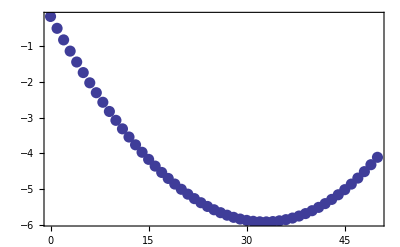

```mathematica
Yc3SigmaPlusNa40K = Yc3SigmaPlusNa39K;
For[i=1,i<10,i++,
For[j=0,j<3,j++,
Yc3SigmaPlusNa40K[[i+1,j+1]]=Yc3SigmaPlusNa39K[[i+1,j+1]](muNa39K/muNa40K)^((i+2j)/2)(1+bc[[i+1,j+1]](Yc3SigmaPlusNa39K[[0+1,1+1]]/Yc3SigmaPlusNa39K[[1+1,0+1]])^2(muNa39K-muNa40K)/muNa40K)
]]
Y=Yc3SigmaPlusNa40K;
mu = muNa40K;
Boundstatesc3SigmaPlusNa40K = Table[{v,e[v]},{v,0,50}];
PAlinesc3SigmaPlusNa40K =Table[{v,Tec3sigmaplus - DeX+Boundstatesc3SigmaPlusNa40K[[v+1,2]]},{v,0,50}];
PAwavelengthc3SigmaPlusNa40K = Table[{v,1/100/PAlinesc3SigmaPlusNa40K[[v+1,2]] 10^9},{v,0,50}];
Isotopeshiftc3SigmaPlusNa40K = Table[{v,Boundstatesc3SigmaPlusNa40K[[v+1,2]]-Boundstatesc3SigmaPlusNa39K[[v+1,2]]},{v,0,50}];
ListPlot[Isotopeshiftc3SigmaPlusNa40K] (*Plotting the isotope shift from the PA lines for 40K... on the order of few wavenumbers *)
```

CompiledFunction::cfsa: Argument 0.5`  + v at position 1 should be a machine-size real number.

General::stop: Further output of CompiledFunction will be suppressed during this calculation.

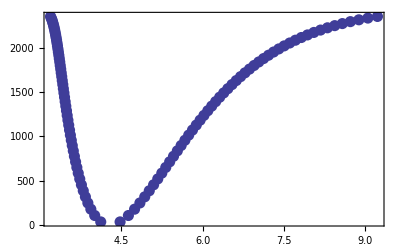

```mathematica
c3SigmaPlusNa40Kpot=Table[{v,e[v],a[v],b[v]},{v,0,50}];
InnerTurningPoint=Table[{c3SigmaPlusNa40Kpot[[i,3]] 10^-10 ,c3SigmaPlusNa40Kpot[[i,2]]},{i,1,51}]; 
OuterTurningPoint=Table[{c3SigmaPlusNa40Kpot[[i,4]] 10^-10 ,c3SigmaPlusNa40Kpot[[i,2]]},{i,1,51}];
c3SigmaPlusNa40KpotR=Sort[Flatten[Join[{InnerTurningPoint,OuterTurningPoint}],1]];
ListPlot[c3SigmaPlusNa40KpotR]
```

### Do mass scaling for Na41K

```mathematica
(*Including simple and fancy mass scaling... for 41K in the c-triplet-sigma-plus potential*)
```

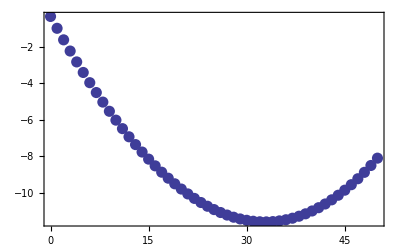

```mathematica
Yc3SigmaPlusNa41K = Yc3SigmaPlusNa39K;
For[i=1,i<10,i++,
For[j=0,j<3,j++,
Yc3SigmaPlusNa41K[[i+1,j+1]]=Yc3SigmaPlusNa39K[[i+1,j+1]](muNa39K/muNa41K)^((i+2j)/2)(1+bc[[i+1,j+1]](Yc3SigmaPlusNa39K[[0+1,1+1]]/Yc3SigmaPlusNa39K[[1+1,0+1]])^2(muNa39K-muNa41K)/muNa41K)
]]
Y=Yc3SigmaPlusNa41K;
mu = muNa41K;
Boundstatesc3SigmaPlusNa41K = Table[{v,e[v]},{v,0,50}];
PAlinesc3SigmaPlusNa41K =Table[{v,Tec3sigmaplus - DeX+Boundstatesc3SigmaPlusNa41K[[v+1,2]]},{v,0,50}];
PAwavelengthc3SigmaPlusNa41K = Table[{v,1/100/PAlinesc3SigmaPlusNa41K[[v+1,2]] 10^9},{v,0,50}];
Isotopeshiftc3SigmaPlusNa41K = Table[{v,Boundstatesc3SigmaPlusNa41K[[v+1,2]]-Boundstatesc3SigmaPlusNa39K[[v+1,2]]},{v,0,50}];
ListPlot[Isotopeshiftc3SigmaPlusNa41K]
```

## b3Π state for Na^39 K R. Ferber et al., J. Chem. Phys. 112, 5740 (2000) http://dx.doi.org/10.1063/1.481149

```mathematica
(*Same story: Dunham coefficients for b-triplett-Pi for Na39K*)
```

```mathematica
mu = muNa39K;
Teb3Pi= 11562.18;
vmaxb3Pi = 75;
Y=Table[0,{i,1,10},{j,1,3}];
Y[[All,All]]=0;
Y[[0+1,0+1]]=0;
Y[[1+1,0+1]]=120.371380;
Y[[2+1,0+1]]=-0.332024;
Y[[3+1,0+1]]=-0.104098 10^-2;
Y[[4+1,0+1]]=0.386127 10^-4;
Y[[5+1,0+1]]=-0.123100 10^-5;
Y[[6+1,0+1]]=0.143700 10^-7;
Y[[7+1,0+1]]=-0.805024 10^-10;
Y[[0+1,1+1]]=0.950673 10^-1;
Y[[1+1,1+1]]=-0.328708 10^-3;
Y[[2+1,1+1]]=-0.205156 10^-5;
Y[[3+1,1+1]]=0.361430 10^-7;
Y[[4+1,1+1]]=-0.186723 10^-8;
Y[[5+1,1+1]]=0.278352 10^-10;
Y[[6+1,1+1]]=-0.235550 10^-12;
Y[[0+1,2+1]]=-0.230157 10^-6;
Y[[1+1,2+1]]=-0.178322 10^-8;
Y[[2+1,2+1]]=0.802326 10^-10;
Y[[3+1,2+1]]=-0.159840 10^-11;
Y//MatrixForm
```

(0 | 0.0950673 | -2.30157×10^-7
120.371 | -0.000328708 | -1.78322×10^-9
-0.332024 | -2.05156×10^-6 | 8.02326×10^-11
-0.00104098 | 3.6143×10^-8 | -1.5984×10^-12
0.0000386127 | -1.86723×10^-9 | 0
-1.231×10^-6 | 2.78352×10^-11 | 0
1.437×10^-8 | -2.3555×10^-13 | 0
-8.05024×10^-11 | 0 | 0
0 | 0 | 0
0 | 0 | 0)

## RKR Potential for b3Π:

```mathematica
(* with the RKR routine that directly gives the energy versus inner/outer turning points*)
```

CompiledFunction::cfsa: Argument 0.5`  + v at position 1 should be a machine-size real number.

General::stop: Further output of CompiledFunction will be suppressed during this calculation.

(0 | 60.1026 | 3.36747 | 3.64615
1 | 179.807 | 3.27455 | 3.75838
2 | 298.838 | 3.21316 | 3.83925
3 | 417.193 | 3.16474 | 3.90731
4 | 534.867 | 3.12392 | 3.96794
5 | 651.855 | 3.08824 | 4.02361
6 | 768.156 | 3.05633 | 4.07568
7 | 883.765 | 3.02734 | 4.125
8 | 998.681 | 3.00069 | 4.17216
9 | 1112.9 | 2.97598 | 4.21757
10 | 1226.42 | 2.9529 | 4.26152
11 | 1339.24 | 2.93123 | 4.30426
12 | 1451.35 | 2.91078 | 4.34597
13 | 1562.75 | 2.8914 | 4.3868
14 | 1673.44 | 2.87299 | 4.42687
15 | 1783.42 | 2.85543 | 4.46629
16 | 1892.68 | 2.83866 | 4.50515
17 | 2001.21 | 2.82259 | 4.54351
18 | 2109.02 | 2.80718 | 4.58145
19 | 2216.09 | 2.79236 | 4.61903
20 | 2322.42 | 2.7781 | 4.65631
21 | 2428. | 2.76435 | 4.69332
22 | 2532.84 | 2.75108 | 4.73011
23 | 2636.91 | 2.73826 | 4.76673
24 | 2740.22 | 2.72586 | 4.80321
25 | 2842.75 | 2.71386 | 4.83959
26 | 2944.5 | 2.70223 | 4.8759
27 | 3045.45 | 2.69096 | 4.91218
28 | 3145.6 | 2.68002 | 4.94846
29 | 3244.93 | 2.66941 | 4.98476
30 | 3343.44 | 2.6591 | 5.02113
31 | 3441.11 | 2.64909 | 5.05758
32 | 3537.93 | 2.63936 | 5.09415
33 | 3633.88 | 2.62989 | 5.13087
34 | 3728.96 | 2.62068 | 5.16777
35 | 3823.14 | 2.61172 | 5.20489
36 | 3916.41 | 2.60301 | 5.24225
37 | 4008.76 | 2.59452 | 5.27988
38 | 4100.16 | 2.58626 | 5.31783
39 | 4190.6 | 2.57822 | 5.35612
40 | 4280.06 | 2.57039 | 5.39479
41 | 4368.52 | 2.56277 | 5.43389
42 | 4455.96 | 2.55535 | 5.47345
43 | 4542.35 | 2.54813 | 5.51352
44 | 4627.68 | 2.5411 | 5.55414
45 | 4711.91 | 2.53427 | 5.59537
46 | 4795.02 | 2.52762 | 5.63726
47 | 4876.98 | 2.52115 | 5.67987
48 | 4957.76 | 2.51487 | 5.72326
49 | 5037.34 | 2.50876 | 5.76749
50 | 5115.68 | 2.50283 | 5.81265
51 | 5192.74 | 2.49708 | 5.85882
52 | 5268.49 | 2.4915 | 5.90608
53 | 5342.89 | 2.48609 | 5.95454
54 | 5415.89 | 2.48085 | 6.00431
55 | 5487.46 | 2.47579 | 6.05551
56 | 5557.55 | 2.47089 | 6.10828
57 | 5626.1 | 2.46616 | 6.16277
58 | 5693.07 | 2.46159 | 6.21915
59 | 5758.4 | 2.45719 | 6.27763
60 | 5822.03 | 2.45294 | 6.33842
61 | 5883.9 | 2.44886 | 6.40178
62 | 5943.93 | 2.44492 | 6.46801
63 | 6002.06 | 2.44113 | 6.53745
64 | 6058.22 | 2.43748 | 6.61049
65 | 6112.32 | 2.43396 | 6.68761
66 | 6164.27 | 2.43054 | 6.76935
67 | 6213.98 | 2.42722 | 6.85639
68 | 6261.36 | 2.42397 | 6.94953
69 | 6306.3 | 2.42075 | 7.04977
70 | 6348.68 | 2.41752 | 7.15834
71 | 6388.41 | 2.41422 | 7.27682
72 | 6425.33 | 2.41074 | 7.40725
73 | 6459.33 | 2.40699 | 7.55235
74 | 6490.27 | 2.40276 | 7.71585
75 | 6517.98 | 2.3978 | 7.90307)

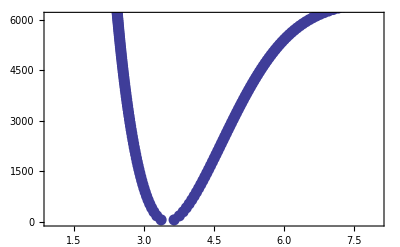

```mathematica
Yb3PiNa39K = Y;
RKRPotb3PiNa39K = Table[{v,e[v],a[v],b[v]},{v,0,vmaxb3Pi}];
Boundstatesb3PiNa39K = Table[{v,e[v]},{v,0,vmaxb3Pi}];
RKRPotb3PiNa39K//MatrixForm
Showb3PiPot=Show[ListPlot[Table[{RKRPotb3PiNa39K[[v,3]],RKRPotb3PiNa39K[[v,2]]},{v,1,vmaxb3Pi+1}]],ListPlot[Table[{RKRPotb3PiNa39K[[v,4]],RKRPotb3PiNa39K[[v,2]]},{v,1,vmaxb3Pi+1}]], PlotRange->{{1,8},{0,6100}}]
```

## Finding energies of Na^40 K and Na^41 K b3Π via mass scaling of Dunham coefficients: Dunham, Phys. Rev. 41, 721 (1932) http://prola.aps.org/abstract/PR/v41/i6/p721_1

```mathematica
(*Including simple and fancy mass scaling... for 40K in the b-triplet-Pi potential*)
```

#### Correction terms to simple mass scaling (essentially negligible for us...)

```mathematica
Y = Yb3PiNa39K;
bc = Y;
bc[[All,All]]=0;
a1 = Y[[1+1,1+1]] Y[[1+1,0+1]]/(6 Y[[0+1,1+1]]^2)-1;
bc[[0+1,1+1]] = Y[[1+1,0+1]]^2 Y[[2+1,1+1]]/(4 Y[[0+1,1+1]]^3)+16 a1 Y[[2+1,0+1]]/(3Y[[0+1,1+1]])-8a1 - 6 a1^2+4 a1^3;
bc[[1+1,0+1]] = 5Y[[1+1,0+1]] Y[[3+1,0+1]]/(4 Y[[0+1,1+1]]^2)+a1 Y[[1+1,0+1]]^2 Y[[2+1,1+1]]/(3 Y[[0+1,1+1]]^3)-10 a1 -20 a1^2-15 a1^3/2-5 a1^4/2+Y[[2+1,0+1]](4 a1 + 16 a1^2/3)/Y[[0+1,1+1]]+Y[[2+1,0+1]]^2/(2 Y[[0+1,1+1]]^2);
bc[[0+1,2+1]] = 73/2+37a1 + 67 a1^2/2+33 a1^3-6 a1^4-9Y[[1+1,0+1]] Y[[3+1,0+1]]/(2 Y[[0+1,1+1]]^2)+Y[[1+1,0+1]]^2 Y[[2+1,1+1]](3-11a1/6)/(2 Y[[0+1,1+1]]^3)-Y[[2+1,0+1]](130/3+4a1+74 a1^2/3)/(2Y[[0+1,1+1]])+31 Y[[2+1,0+1]]^2/(9 Y[[0+1,1+1]]^2);
typicalcorrection = bc[[0+1,1+1]](Yb3PiNa39K[[0+1,1+1]]/Yb3PiNa39K[[1+1,0+1]])^2(muNa39K-muNa40K)/muNa40K
```

7.20121×10^-9

### Do mass scaling for Na40K

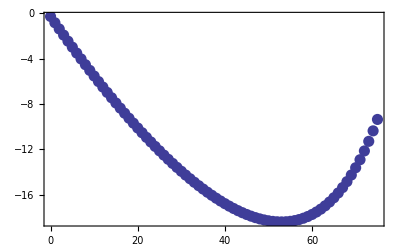

```mathematica
Yb3PiNa40K = Yb3PiNa39K;
For[i=1,i<10,i++,
For[j=0,j<3,j++,
Yb3PiNa40K[[i+1,j+1]]=Yb3PiNa39K[[i+1,j+1]](muNa39K/muNa40K)^((i+2j)/2)(1+bc[[i+1,j+1]](Yb3PiNa39K[[0+1,1+1]]/Yb3PiNa39K[[1+1,0+1]])^2(muNa39K-muNa40K)/muNa40K)
]]
Y=Yb3PiNa40K;
mu = muNa40K;
Boundstatesb3PiNa40K = Table[{v,e[v]},{v,0,vmaxb3Pi}];
PAlinesb3PiNa40K =Table[{v,Teb3Pi - DeX+Boundstatesb3PiNa40K[[v+1,2]]},{v,0,vmaxb3Pi}];
PAwavelengthb3PiNa40K = Table[{v,1/100/PAlinesb3PiNa40K[[v+1,2]] 10^9},{v,0,vmaxb3Pi}];
Isotopeshiftb3PiNa40K = Table[{v,Boundstatesb3PiNa40K[[v+1,2]]-Boundstatesb3PiNa39K[[v+1,2]]},{v,0,vmaxb3Pi}];
ListPlot[Isotopeshiftb3PiNa40K] (*Plotting the isotope shift from the PA lines for 40K... on the order of ten  wavenumbers *)
```

CompiledFunction::cfsa: Argument 0.5`  + v at position 1 should be a machine-size real number.

General::stop: Further output of CompiledFunction will be suppressed during this calculation.

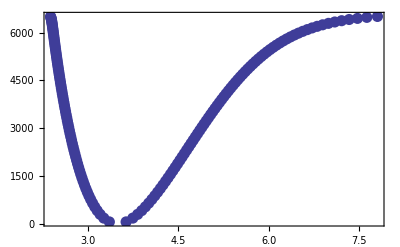

```mathematica
b3PiNa40Kpot=Table[{v,e[v],a[v],b[v]},{v,0,vmaxb3Pi}];
InnerTurningPoint=Table[{b3PiNa40Kpot[[i,3]] 10^-10 ,b3PiNa40Kpot[[i,2]]},{i,1,vmaxb3Pi+1}]; 
OuterTurningPoint=Table[{b3PiNa40Kpot[[i,4]] 10^-10 ,b3PiNa40Kpot[[i,2]]},{i,1,vmaxb3Pi+1}];
b3PiNa40KpotR=Sort[Flatten[Join[{InnerTurningPoint,OuterTurningPoint}],1]];
ListPlot[b3PiNa40KpotR]
```

### Do mass scaling for Na41K

```mathematica
(*Including simple and fancy mass scaling... for 41K in the b-triplet-Pi potential*)
```

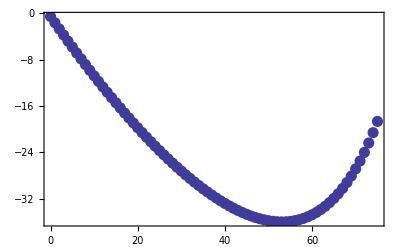

```mathematica
Yb3PiNa41K = Yb3PiNa39K;
For[i=1,i<10,i++,
For[j=0,j<3,j++,
Yb3PiNa41K[[i+1,j+1]]=Yb3PiNa39K[[i+1,j+1]](muNa39K/muNa41K)^((i+2j)/2)(1+bc[[i+1,j+1]](Yb3PiNa39K[[0+1,1+1]]/Yb3PiNa39K[[1+1,0+1]])^2(muNa39K-muNa41K)/muNa41K)
]]
Y=Yb3PiNa41K;
mu = muNa41K;
Boundstatesb3PiNa41K = Table[{v,e[v]},{v,0,vmaxb3Pi}];
PAlinesb3PiNa41K =Table[{v,Teb3Pi - DeX+Boundstatesb3PiNa41K[[v+1,2]]},{v,0,vmaxb3Pi}];
PAwavelengthb3PiNa41K = Table[{v,1/100/PAlinesb3PiNa41K[[v+1,2]] 10^9},{v,0,vmaxb3Pi}];
Isotopeshiftb3PiNa41K = Table[{v,Boundstatesb3PiNa41K[[v+1,2]]-Boundstatesb3PiNa39K[[v+1,2]]},{v,0,vmaxb3Pi}];
ListPlot[Isotopeshiftb3PiNa41K]
```

## A1Σ+ state for Na^39 K Ross, Clements, Barrow, J. Mol. Spec. 127, 546 (1988)

```mathematica
(*Same story: Dunham coefficients for A-singlet-sigma-plus for Na39K*)
```

```mathematica
mu = muNa39K;
TeA1SigmaPlus= 12137.272;
vmaxA1SigmaPlus = 100;
Y=Table[0,{i,1,10},{j,1,3}];
Y[[All,All]]=0;
Y[[0+1,0+1]]=0;
Y[[1+1,0+1]]=81.250506;
Y[[2+1,0+1]]=-0.27470815;
Y[[3+1,0+1]]=0.41931994 10^-2;
Y[[4+1,0+1]]=-0.7720508 10^-4;
Y[[5+1,0+1]]=0.6932446 10^-6;
Y[[6+1,0+1]]=-0.282698 10^-8;
Y[[0+1,1+1]]=0.0661371;
Y[[1+1,1+1]]=-0.360162 10^-3;
Y[[2+1,1+1]]=0.3300504 10^-5;
Y[[3+1,1+1]]=-0.3409183 10^-7;
Y[[0+1,2+1]]=0.16600 10^-6;
Y[[1+1,2+1]]=-0.6343 10^-9;
Y//MatrixForm
```

(0 | 0.0661371 | 1.66×10^-7
81.2505 | -0.000360162 | -6.343×10^-10
-0.274708 | 3.3005×10^-6 | 0
0.0041932 | -3.40918×10^-8 | 0
-0.0000772051 | 0 | 0
6.93245×10^-7 | 0 | 0
-2.82698×10^-9 | 0 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)

## RKR Potential for A1Σ+:

CompiledFunction::cfsa: Argument 0.5`  + v at position 1 should be a machine-size real number.

General::stop: Further output of CompiledFunction will be suppressed during this calculation.

(0 | 40.5571 | 4.03624 | 4.37553
1 | 121.271 | 3.92568 | 4.51495
2 | 201.472 | 3.85334 | 4.6161
3 | 281.18 | 3.79669 | 4.7015
4 | 360.416 | 3.74918 | 4.77768
5 | 439.198 | 3.70785 | 4.84763
6 | 517.543 | 3.67103 | 4.913
7 | 595.467 | 3.63769 | 4.97482
8 | 672.983 | 3.60715 | 5.03379
9 | 750.105 | 3.5789 | 5.09039
10 | 826.844 | 3.55258 | 5.145
11 | 903.211 | 3.52792 | 5.1979
12 | 979.214 | 3.50469 | 5.24931
13 | 1054.86 | 3.48272 | 5.2994
14 | 1130.16 | 3.46186 | 5.34833
15 | 1205.12 | 3.442 | 5.39622
16 | 1279.75 | 3.42303 | 5.44317
17 | 1354.04 | 3.40487 | 5.48928
18 | 1428.01 | 3.38746 | 5.53461
19 | 1501.66 | 3.37071 | 5.57925
20 | 1574.98 | 3.35459 | 5.62325
21 | 1647.98 | 3.33904 | 5.66666
22 | 1720.67 | 3.32402 | 5.70954
23 | 1793.04 | 3.3095 | 5.75192
24 | 1865.1 | 3.29543 | 5.79386
25 | 1936.84 | 3.28179 | 5.83539
26 | 2008.27 | 3.26856 | 5.87654
27 | 2079.37 | 3.2557 | 5.91735
28 | 2150.16 | 3.2432 | 5.95785
29 | 2220.63 | 3.23103 | 5.99806
30 | 2290.78 | 3.21919 | 6.03802
31 | 2360.6 | 3.20764 | 6.07774
32 | 2430.1 | 3.19639 | 6.11725
33 | 2499.26 | 3.18541 | 6.15659
34 | 2568.1 | 3.17469 | 6.19576
35 | 2636.6 | 3.16422 | 6.23478
36 | 2704.76 | 3.15399 | 6.27369
37 | 2772.58 | 3.14399 | 6.3125
38 | 2840.06 | 3.13422 | 6.35123
39 | 2907.18 | 3.12466 | 6.3899
40 | 2973.96 | 3.11531 | 6.42853
41 | 3040.37 | 3.10616 | 6.46713
42 | 3106.43 | 3.0972 | 6.50572
43 | 3172.12 | 3.08844 | 6.54432
44 | 3237.43 | 3.07986 | 6.58296
45 | 3302.38 | 3.07146 | 6.62163
46 | 3366.94 | 3.06323 | 6.66038
47 | 3431.12 | 3.05518 | 6.6992
48 | 3494.9 | 3.0473 | 6.73812
49 | 3558.3 | 3.03958 | 6.77716
50 | 3621.28 | 3.03202 | 6.81634
51 | 3683.87 | 3.02463 | 6.85566
52 | 3746.03 | 3.01739 | 6.89516
53 | 3807.78 | 3.0103 | 6.93486
54 | 3869.1 | 3.00336 | 6.97476
55 | 3929.99 | 2.99658 | 7.0149
56 | 3990.44 | 2.98994 | 7.0553
57 | 4050.43 | 2.98344 | 7.09597
58 | 4109.97 | 2.97709 | 7.13694
59 | 4169.05 | 2.97088 | 7.17824
60 | 4227.65 | 2.9648 | 7.2199
61 | 4285.76 | 2.95886 | 7.26193
62 | 4343.38 | 2.95305 | 7.30437
63 | 4400.5 | 2.94738 | 7.34726
64 | 4457.09 | 2.94183 | 7.39062
65 | 4513.17 | 2.9364 | 7.43449
66 | 4568.69 | 2.9311 | 7.47891
67 | 4623.67 | 2.92591 | 7.52392
68 | 4678.08 | 2.92084 | 7.56956
69 | 4731.9 | 2.91587 | 7.61588
70 | 4785.12 | 2.91101 | 7.66293
71 | 4837.72 | 2.90625 | 7.71078
72 | 4889.69 | 2.90158 | 7.75946
73 | 4941.01 | 2.897 | 7.80906
74 | 4991.64 | 2.8925 | 7.85965
75 | 5041.59 | 2.88807 | 7.9113
76 | 5090.81 | 2.88371 | 7.96409
77 | 5139.29 | 2.8794 | 8.01812
78 | 5187. | 2.87513 | 8.07349
79 | 5233.91 | 2.8709 | 8.13033
80 | 5279.99 | 2.86668 | 8.18874
81 | 5325.22 | 2.86246 | 8.24887
82 | 5369.56 | 2.85823 | 8.31088
83 | 5412.98 | 2.85397 | 8.37494
84 | 5455.43 | 2.84966 | 8.44124
85 | 5496.89 | 2.84526 | 8.51001
86 | 5537.32 | 2.84077 | 8.58149
87 | 5576.66 | 2.83613 | 8.65597
88 | 5614.88 | 2.83132 | 8.73378
89 | 5651.92 | 2.8263 | 8.81528
90 | 5687.75 | 2.82102 | 8.90092
91 | 5722.3 | 2.81541 | 8.99119
92 | 5755.53 | 2.80943 | 9.08672
93 | 5787.37 | 2.80298 | 9.1882
94 | 5817.77 | 2.79598 | 9.29651
95 | 5846.65 | 2.78831 | 9.41269
96 | 5873.97 | 2.77983 | 9.53805
97 | 5899.64 | 2.77037 | 9.67421
98 | 5923.59 | 2.75971 | 9.82327
99 | 5945.74 | 2.74756 | 9.98798
100 | 5966.03 | 2.73354 | 10.172)

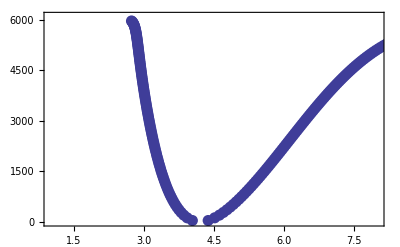

```mathematica
YA1SigmaPlusNa39K = Y;
RKRPotA1SigmaPlusNa39K = Table[{v,e[v],a[v],b[v]},{v,0,vmaxA1SigmaPlus}];
BoundstatesA1SigmaPlusNa39K = Table[{v,e[v]},{v,0,vmaxA1SigmaPlus}];
RKRPotA1SigmaPlusNa39K//MatrixForm
ShowA1SigmaPlusPot=Show[ListPlot[Table[{RKRPotA1SigmaPlusNa39K[[v,3]],RKRPotA1SigmaPlusNa39K[[v,2]]},{v,1,vmaxA1SigmaPlus+1}]],ListPlot[Table[{RKRPotA1SigmaPlusNa39K[[v,4]],RKRPotA1SigmaPlusNa39K[[v,2]]},{v,1,vmaxA1SigmaPlus+1}]], PlotRange->{{1,8},{0,6100}}]
```

## Finding energies of Na^40 K and Na^41 K A1Σ+ via mass scaling of Dunham coefficients: Dunham, Phys. Rev. 41, 721 (1932) http://prola.aps.org/abstract/PR/v41/i6/p721_1

#### Correction terms to simple mass scaling (essentially negligible for us...)

```mathematica
Y = YA1SigmaPlusNa39K;
bc = Y;
bc[[All,All]]=0;
a1 = Y[[1+1,1+1]] Y[[1+1,0+1]]/(6 Y[[0+1,1+1]]^2)-1;
bc[[0+1,1+1]] = Y[[1+1,0+1]]^2 Y[[2+1,1+1]]/(4 Y[[0+1,1+1]]^3)+16 a1 Y[[2+1,0+1]]/(3Y[[0+1,1+1]])-8a1 - 6 a1^2+4 a1^3;
bc[[1+1,0+1]] = 5Y[[1+1,0+1]] Y[[3+1,0+1]]/(4 Y[[0+1,1+1]]^2)+a1 Y[[1+1,0+1]]^2 Y[[2+1,1+1]]/(3 Y[[0+1,1+1]]^3)-10 a1 -20 a1^2-15 a1^3/2-5 a1^4/2+Y[[2+1,0+1]](4 a1 + 16 a1^2/3)/Y[[0+1,1+1]]+Y[[2+1,0+1]]^2/(2 Y[[0+1,1+1]]^2);
bc[[0+1,2+1]] = 73/2+37a1 + 67 a1^2/2+33 a1^3-6 a1^4-9Y[[1+1,0+1]] Y[[3+1,0+1]]/(2 Y[[0+1,1+1]]^2)+Y[[1+1,0+1]]^2 Y[[2+1,1+1]](3-11a1/6)/(2 Y[[0+1,1+1]]^3)-Y[[2+1,0+1]](130/3+4a1+74 a1^2/3)/(2Y[[0+1,1+1]])+31 Y[[2+1,0+1]]^2/(9 Y[[0+1,1+1]]^2);
typicalcorrection = bc[[0+1,1+1]](YA1SigmaPlusNa39K[[0+1,1+1]]/YA1SigmaPlusNa39K[[1+1,0+1]])^2(muNa39K-muNa40K)/muNa40K
```

-1.10272×10^-7

### Do mass scaling for Na40K

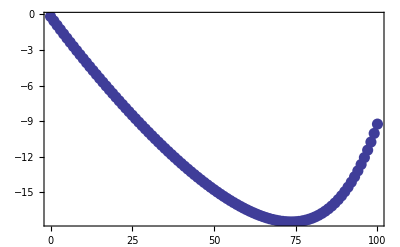

```mathematica
YA1SigmaPlusNa40K = YA1SigmaPlusNa39K;
For[i=1,i<10,i++,
For[j=0,j<3,j++,
YA1SigmaPlusNa40K[[i+1,j+1]]=YA1SigmaPlusNa39K[[i+1,j+1]](muNa39K/muNa40K)^((i+2j)/2)(1+bc[[i+1,j+1]](YA1SigmaPlusNa39K[[0+1,1+1]]/YA1SigmaPlusNa39K[[1+1,0+1]])^2(muNa39K-muNa40K)/muNa40K)
]]
Y=YA1SigmaPlusNa40K;
mu = muNa40K;
BoundstatesA1SigmaPlusNa40K = Table[{v,e[v]},{v,0,vmaxA1SigmaPlus}];
PAlinesA1SigmaPlusNa40K =Table[{v,TeA1SigmaPlus - DeX+BoundstatesA1SigmaPlusNa40K[[v+1,2]]},{v,0,vmaxA1SigmaPlus}];
PAwavelengthA1SigmaPlusNa40K = Table[{v,1/100/PAlinesA1SigmaPlusNa40K[[v+1,2]] 10^9},{v,0,vmaxA1SigmaPlus}];
IsotopeshiftA1SigmaPlusNa40K = Table[{v,BoundstatesA1SigmaPlusNa40K[[v+1,2]]-BoundstatesA1SigmaPlusNa39K[[v+1,2]]},{v,0,vmaxA1SigmaPlus}];
ListPlot[IsotopeshiftA1SigmaPlusNa40K]
```

CompiledFunction::cfsa: Argument 0.5`  + v at position 1 should be a machine-size real number.

General::stop: Further output of CompiledFunction will be suppressed during this calculation.

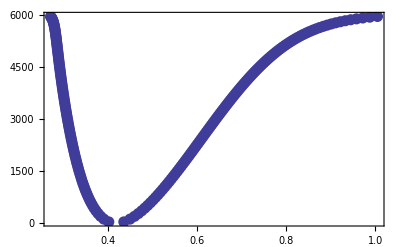

```mathematica
A1SigmaPlusNa40Kpot=Table[{v,e[v],a[v],b[v]},{v,0,vmaxA1SigmaPlus}];
InnerTurningPoint=Table[{A1SigmaPlusNa40Kpot[[i,3]] 10^-10 ,A1SigmaPlusNa40Kpot[[i,2]]},{i,1,vmaxA1SigmaPlus+1}]; 
OuterTurningPoint=Table[{A1SigmaPlusNa40Kpot[[i,4]] 10^-10 ,A1SigmaPlusNa40Kpot[[i,2]]},{i,1,vmaxA1SigmaPlus+1}];
A1SigmaPlusNa40KpotR=Sort[Flatten[Join[{InnerTurningPoint,OuterTurningPoint}],1]];
ListPlot[A1SigmaPlusNa40KpotR]
```

### Do mass scaling for Na41K

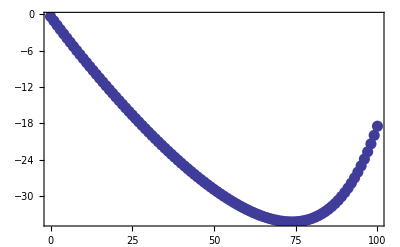

```mathematica
YA1SigmaPlusNa41K = YA1SigmaPlusNa39K;
For[i=1,i<10,i++,
For[j=0,j<3,j++,
YA1SigmaPlusNa41K[[i+1,j+1]]=YA1SigmaPlusNa39K[[i+1,j+1]](muNa39K/muNa41K)^((i+2j)/2)(1+bc[[i+1,j+1]](YA1SigmaPlusNa39K[[0+1,1+1]]/YA1SigmaPlusNa39K[[1+1,0+1]])^2(muNa39K-muNa41K)/muNa41K)
]]
Y=YA1SigmaPlusNa41K;
mu = muNa41K;
BoundstatesA1SigmaPlusNa41K = Table[{v,e[v]},{v,0,vmaxA1SigmaPlus}];
PAlinesA1SigmaPlusNa41K =Table[{v,TeA1SigmaPlus - DeX+BoundstatesA1SigmaPlusNa41K[[v+1,2]]},{v,0,vmaxA1SigmaPlus}];
PAwavelengthA1SigmaPlusNa41K = Table[{v,1/100/PAlinesA1SigmaPlusNa41K[[v+1,2]] 10^9},{v,0,vmaxA1SigmaPlus}];
IsotopeshiftA1SigmaPlusNa41K = Table[{v,BoundstatesA1SigmaPlusNa41K[[v+1,2]]-BoundstatesA1SigmaPlusNa39K[[v+1,2]]},{v,0,vmaxA1SigmaPlus}];
ListPlot[IsotopeshiftA1SigmaPlusNa41K]
```

# Summary of all the potentials :

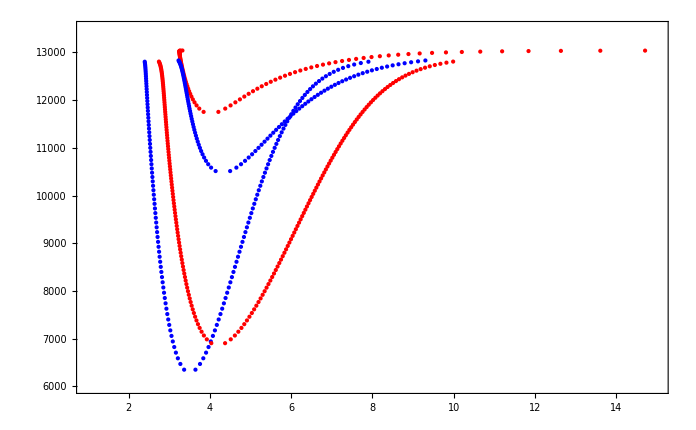

```mathematica
Show[ListPlot[Table[{RKRPotB1PiNa39K[[v,3]],RKRPotB1PiNa39K[[v,2]]+TeB1Pi-DeX},{v,1,44}],PlotStyle->{Red}],ListPlot[Table[{RKRPotB1PiNa39K[[v,4]],RKRPotB1PiNa39K[[v,2]]+TeB1Pi-DeX},{v,1,44}],PlotStyle->{Red}],
ListPlot[Table[{RKRPotc3SigmaPlusNa39K[[v,3]],RKRPotc3SigmaPlusNa39K[[v,2]]+Tec3sigmaplus-DeX},{v,1,vmaxc3SigmaPlus+1}],PlotStyle->{Blue}],
ListPlot[Table[{RKRPotc3SigmaPlusNa39K[[v,4]],RKRPotc3SigmaPlusNa39K[[v,2]]+Tec3sigmaplus-DeX},{v,1,vmaxc3SigmaPlus+1}],PlotStyle->{Blue}],
ListPlot[Table[{RKRPotb3PiNa39K[[v,3]],RKRPotb3PiNa39K[[v,2]]+Teb3Pi-DeX},{v,1,vmaxb3Pi+1}],PlotStyle->{Blue}],
ListPlot[Table[{RKRPotb3PiNa39K[[v,4]],RKRPotb3PiNa39K[[v,2]]+Teb3Pi-DeX},{v,1,vmaxb3Pi+1}],PlotStyle->{Blue}],
ListPlot[Table[{RKRPotA1SigmaPlusNa39K[[v,3]],RKRPotA1SigmaPlusNa39K[[v,2]]+TeA1SigmaPlus-DeX},{v,1,vmaxA1SigmaPlus}],PlotStyle->{Red}],
ListPlot[Table[{RKRPotA1SigmaPlusNa39K[[v,4]],RKRPotA1SigmaPlusNa39K[[v,2]]+TeA1SigmaPlus-DeX},{v,1,vmaxA1SigmaPlus}],PlotStyle->{Red}],PlotRange->{{1,15},{6000,13500}}]
```

```mathematica
FoundLines=-{772.366,772.951,774.362,775.191,777.017,778.045,779.824,781.522,782.881,784.25,785.66,785.75,787.27,788.87,790.58,790.97,792.311,
794.17,796.11,796.151,800.22,802.381,802.394,804.556,804.574,804.603,810.966,813.701,817.59,819.705,820.1,820.11,820.155,820.165,829.22,832.42,835.819,839.091}
(*FoundLinesOld=-{772.366,772.951,774.362,775.191,777.017,778.045,779.824,781.522,782.881,784.25,785.66,785.75,787.27,788.87,790.58,790.97,792.311,794.17,796.151,800.194,800.209,800.22,800.231,802.381,802.394,804.556,804.574,804.603,810.966,813.701,817.59,819.705,829.121,832.42};*)
Wavelengthgrid=Plot[-760,{x,0,2},PlotRange->{-760,-850},Frame->True];
GraphicsFoundLines=Graphics[Table[{Directive[Thin,Black],Line[{{0,FoundLines[[i]]},{5,FoundLines[[i]]}}]},{i,1,Dimensions[FoundLines][[1]]}]];
GraphicsPAc3SigmaPlusNa40K =Graphics[Table[{Directive[Thick,Blue],Line[{{1.8,-PAwavelengthc3SigmaPlusNa40K[[i,2]]},{2.2,-PAwavelengthc3SigmaPlusNa40K[[i,2]]}}]},{i,1,Dimensions[PAwavelengthc3SigmaPlusNa40K][[1]]}]];
GraphicsPAB1PiNa40K = Graphics[Table[{Directive[Thick,Red],Line[{{0.8,-PAwavelengthB1PiNa40K[[i,2]]},{1.2,-PAwavelengthB1PiNa40K[[i,2]]}}]},{i,1,Dimensions[PAwavelengthB1PiNa40K][[1]]}]];
GraphicsPAb3PiNa40K = Graphics[Table[{Directive[Thick,Blue],Line[{{2.8,-PAwavelengthb3PiNa40K[[i,2]]},{3.2,-PAwavelengthb3PiNa40K[[i,2]]}}]},{i,1,Dimensions[PAwavelengthb3PiNa40K][[1]]}]];
GraphicsPAA1SigmaPlusNa40K = Graphics[Table[{Directive[Thick,Red],Line[{{3.8,-PAwavelengthA1SigmaPlusNa40K[[i,2]]},{4.2,-PAwavelengthA1SigmaPlusNa40K[[i,2]]}}]},{i,1,Dimensions[PAwavelengthA1SigmaPlusNa40K][[1]]}]];
```

{-772.366,-772.951,-774.362,-775.191,-777.017,-778.045,-779.824,-781.522,-782.881,-784.25,-785.66,-785.75,-787.27,-788.87,-790.58,-790.97,-792.311,-794.17,-796.11,-796.151,-800.22,-802.381,-802.394,-804.556,-804.574,-804.603,-810.966,-813.701,-817.59,-819.705,-820.1,-820.11,-820.155,-820.165,-829.22,-832.42,-835.819,-839.091}

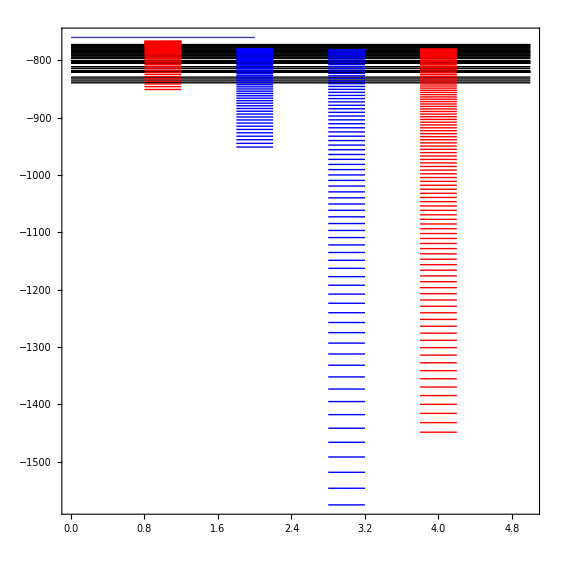

```mathematica
Show[Wavelengthgrid,GraphicsFoundLines,GraphicsPAc3SigmaPlusNa40K,GraphicsPAB1PiNa40K,GraphicsPAb3PiNa40K,GraphicsPAA1SigmaPlusNa40K,PlotRange->{{0.5,4.5},{-766,-822}},AspectRatio->1]
```

```mathematica
PAwavelengthc3SigmaPlusNa40K[[26]]
PAwavelengthB1PiNa40K[[5]]
PAlinesc3SigmaPlusNa40K[[26]]
PAlinesB1PiNa40K[[5]]
```

{25,832.321}

{4,832.257}

{25,12014.6}

{4,12015.5}

```mathematica
1/100/(PAlinesc3SigmaPlusNa40K[[26,2]]+5211.75)*10^9
1/100/(PAlinesB1PiNa40K[[5,2]]+5211.75)*10^9
```

580.506

580.475

```mathematica
TableForm[Table[{v,PAlinesB1PiNa40K[[v+1,2]],PAwavelengthB1PiNa40K[[v+1,2]]},{v,0,vmaxB1Pi}]];
TableForm[Table[{v,PAlinesc3SigmaPlusNa40K[[v+1,2]],PAwavelengthc3SigmaPlusNa40K[[v+1,2]]},{v,0,vmaxc3SigmaPlus}]];
TableForm[Table[{v,PAlinesb3PiNa40K[[v+1,2]],PAwavelengthb3PiNa40K[[v+1,2]]},{v,0,vmaxb3Pi}]];
TableForm[Table[{v,PAlinesA1SigmaPlusNa40K[[v+1,2]],PAwavelengthA1SigmaPlusNa40K[[v+1,2]]},{v,0,vmaxA1SigmaPlus}]];
```

# Calculation of Wavefunctions for B1Π:

### Interpolation of B1Π RKR potential :

```mathematica
B1PiInt=ListInterpolation[Transpose[B1PiNa40KpotR][[2]],{Transpose[B1PiNa40KpotR][[1]]},InterpolationOrder->7]
eint=Table[B1PiInt[B1PiNa40KpotR[[i,1]]],{i,1,Dimensions[B1PiNa40KpotR][[1]]}]
eRKR=Transpose[B1PiNa40KpotR][[2]];
Δe=eRKR-eint;
```

InterpolatingFunction[{{3.19315×10^-10,1.54533×10^-9}},<>]

{1317.51,1314.24,1309.98,1320.01,1304.59,1298.,1290.16,1281.07,1270.72,1259.14,1246.33,1232.31,1217.07,1200.63,1182.98,1322.06,1164.09,1143.96,1122.55,1099.82,1075.76,1050.3,1023.41,995.044,965.148,933.675,900.57,865.782,829.255,790.934,750.761,708.678,664.626,618.547,570.381,520.071,467.563,412.806,355.755,296.375,234.638,170.531,104.058,35.2362,35.2362,104.058,170.531,234.638,296.375,355.755,412.806,467.563,520.071,570.381,618.547,664.626,708.678,750.761,790.934,829.255,865.782,900.57,933.675,965.148,995.044,1023.41,1050.3,1075.76,1099.82,1122.55,1143.96,1164.09,1182.98,1200.63,1217.07,1232.31,1246.33,1259.14,1270.72,1281.07,1290.16,1298.,1304.59,1309.98,1314.24,1317.51,1320.01,1322.06}

```mathematica
lowcut=3.25 10^-10;
highcut=13 10^-10 ;
B1PiIntBox[x_]:=Piecewise[{{B1PiInt[lowcut]-10^-11(x-lowcut),x≤lowcut},{B1PiInt[x],lowcut<x<highcut},{B1PiInt[highcut]+(x-highcut)^4,x≥highcut}}];
```

```mathematica
eintbox=Table[{B1PiNa40KpotR[[i,1]],B1PiIntBox[B1PiNa40KpotR[[i,1]]]},{i,1,Dimensions[B1PiNa40KpotR][[1]]}];
ListLinePlot[eintbox,PlotRange->All,PlotStyle->Red,Frame->True];
```

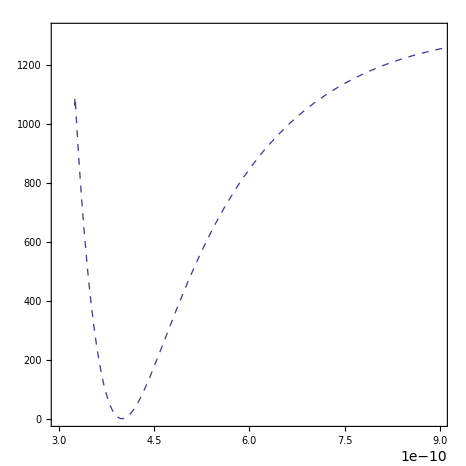

```mathematica
ppotB1Pi=Plot[B1PiInt[x]+0TeB1Pi- 0DeX,{x,3.25 10^-10,13 10^-10},AspectRatio->1,PlotRange->{{3. 10^-10,9. 10^-10},All},PlotStyle->Directive[Dashed,Thickness[0.002]]]
Plot[B1PiIntBox[x],{x,3.25 10^-10,13 10^-10},AspectRatio->1,PlotRange->{All,{1000,1400}}];
```

### Interpolation of c3Σ+ RKR potential :

```mathematica
c3SigmaPlusInt=ListInterpolation[Transpose[c3SigmaPlusNa40KpotR][[2]],{Transpose[c3SigmaPlusNa40KpotR][[1]]},InterpolationOrder->7]
eint=Table[B1PiInt[c3SigmaPlusNa40KpotR[[i,1]]],{i,1,Dimensions[c3SigmaPlusNa40KpotR][[1]]}]
eRKR=Transpose[c3SigmaPlusNa40KpotR][[2]];
Δe=eRKR-eint;
```

InterpolatingFunction[{{3.19656×10^-10,9.2255×10^-10}},<>]

{1268.78,1285.11,1228.47,1288.56,1284.53,1098.54,1062.02,1027.94,995.491,964.434,934.576,905.755,877.828,850.664,824.144,798.162,772.618,747.426,722.504,697.782,673.196,648.688,624.21,599.716,575.168,550.532,525.782,500.894,475.852,450.644,425.263,399.711,373.995,348.129,322.136,296.048,269.911,243.779,217.725,191.841,166.239,141.063,116.495,92.7672,70.1886,49.1748,30.3137,14.5509,3.45901,0.331176,15.9347,164.904,248.693,312.1,366.05,413.918,457.344,497.295,534.408,569.134,601.811,632.7,662.007,689.902,716.525,741.994,766.408,789.853,812.404,834.126,855.076,875.305,894.857,913.774,932.091,949.841,967.053,983.753,999.965,1015.71,1031.01,1045.88,1060.34,1074.41,1088.08,1101.38,1114.31,1126.89,1139.11,1150.98,1162.51,1173.68,1184.51,1194.99,1205.11,1214.87,1224.25,1233.25,1241.86,1250.06,1257.84,1265.19}

```mathematica
lowcut=3.25 10^-10;
highcut=13 10^-10 ;
c3SigmaPlusIntBox[x_]:=Piecewise[{{c3SigmaPlusInt[lowcut]-10^-11(x-lowcut),x≤lowcut},{c3SigmaPlusInt[x],lowcut<x<highcut},{c3SigmaPlusInt[highcut]+(x-highcut)^4,x≥highcut}}];
```

```mathematica
eintbox=Table[{c3SigmaPlusNa40KpotR[[i,1]],B1PiIntBox[c3SigmaPlusNa40KpotR[[i,1]]]},{i,1,Dimensions[c3SigmaPlusNa40KpotR][[1]]}];
ListLinePlot[eintbox,PlotRange->All,PlotStyle->Red,Frame->True];
```

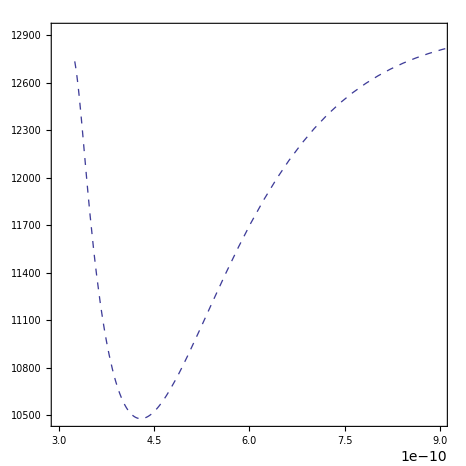

```mathematica
ppotc3SigmaPlus=Plot[c3SigmaPlusInt[x]+Tec3sigmaplus-DeX,{x,3.25 10^-10,13 10^-10},AspectRatio->1,PlotRange->{{3. 10^-10,9. 10^-10},All},PlotStyle->Directive[Dashed,Thickness[0.002]]]
Plot[c3SigmaPlusIntBox[x],{x,3.25 10^-10,13 10^-10},AspectRatio->1,PlotRange->{All,All}];
```

### Interpolation of b3Π RKR potential :

```mathematica
b3PiInt=ListInterpolation[Transpose[b3PiNa40KpotR][[2]],{Transpose[b3PiNa40KpotR][[1]]},InterpolationOrder->7]
eint=Table[b3PiInt[b3PiNa40KpotR[[i,1]]],{i,1,Dimensions[b3PiNa40KpotR][[1]]}]
eRKR=Transpose[b3PiNa40KpotR][[2]];
Δe=eRKR-eint;
```

InterpolatingFunction[{{2.37356×10^-10,7.80805×10^-10}},<>]

{6508.62,6479.9,6448.04,6413.19,6375.49,6335.06,6292.03,6246.51,6198.61,6148.42,6096.05,6041.57,5985.09,5926.66,5866.37,5804.29,5740.48,5675.,5607.91,5539.26,5469.11,5397.51,5324.49,5250.1,5174.39,5097.38,5019.12,4939.63,4858.96,4777.13,4694.16,4610.09,4524.95,4438.75,4351.52,4263.28,4174.05,4083.85,3992.71,3900.63,3807.64,3713.75,3618.98,3523.34,3426.84,3329.51,3231.34,3132.36,3032.57,2931.99,2830.62,2728.48,2625.57,2521.89,2417.47,2312.3,2206.4,2099.76,1992.4,1884.31,1775.51,1666.,1555.77,1444.84,1333.22,1220.89,1107.86,994.148,879.741,764.647,648.869,532.409,415.27,297.457,178.973,59.8232,59.8232,178.973,297.457,415.27,532.409,648.869,764.647,879.741,994.148,1107.86,1220.89,1333.22,1444.84,1555.77,1666.,1775.51,1884.31,1992.4,2099.76,2206.4,2312.3,2417.47,2521.89,2625.57,2728.48,2830.62,2931.99,3032.57,3132.36,3231.34,3329.51,3426.84,3523.34,3618.98,3713.75,3807.64,3900.63,3992.71,4083.85,4174.05,4263.28,4351.52,4438.75,4524.95,4610.09,4694.16,4777.13,4858.96,4939.63,5019.12,5097.38,5174.39,5250.1,5324.49,5397.51,5469.11,5539.26,5607.91,5675.,5740.48,5804.29,5866.37,5926.66,5985.09,6041.57,6096.05,6148.42,6198.61,6246.51,6292.03,6335.06,6375.49,6413.19,6448.04,6479.9,6508.62}

```mathematica
lowcut=2.4 10^-10;
highcut=12 10^-10 ;
b3PiIntBox[x_]:=Piecewise[{{b3PiInt[lowcut]-10^-11(x-lowcut),x≤lowcut},{b3PiInt[x],lowcut<x<highcut},{b3PiInt[highcut]+(x-highcut)^4,x≥highcut}}];
```

```mathematica
eintbox=Table[{b3PiNa40KpotR[[i,1]],b3PiIntBox[b3PiNa40KpotR[[i,1]]]},{i,1,Dimensions[b3PiNa40KpotR][[1]]}];
ListLinePlot[eintbox,PlotRange->All,PlotStyle->Red,Frame->True];
```

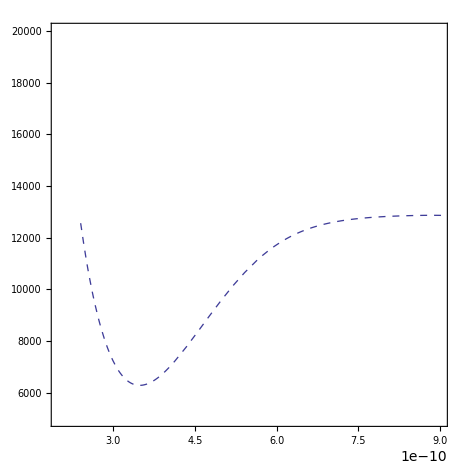

```mathematica
ppotb3Pi=Plot[b3PiInt[x]+Teb3Pi-DeX,{x,2.4 10^-10,13 10^-10},AspectRatio->1,PlotRange->{{2. 10^-10,9. 10^-10},{5000,20000}},PlotStyle->Directive[Dashed,Thickness[0.002]]]
Plot[b3PiIntBox[x],{x,2.4 10^-10,12 10^-10},AspectRatio->1,PlotRange->{All,All}];
```

### Interpolation of A1SigmaPlus RKR potential :

```mathematica
A1SigmaPlusInt=ListInterpolation[Transpose[A1SigmaPlusNa40KpotR][[2]],{Transpose[A1SigmaPlusNa40KpotR][[1]]},InterpolationOrder->7]
eint=Table[A1SigmaPlusInt[A1SigmaPlusNa40KpotR[[i,1]]],{i,1,Dimensions[A1SigmaPlusNa40KpotR][[1]]}]
eRKR=Transpose[A1SigmaPlusNa40KpotR][[2]];
Δe=eRKR-eint;
```

InterpolatingFunction[{{2.70908×10^-10,1.00519×10^-9}},<>]

{5956.78,5935.71,5912.83,5888.2,5861.9,5834.01,5804.58,5773.69,5741.39,5707.75,5672.81,5636.64,5599.27,5560.77,5521.17,5480.52,5438.85,5396.22,5352.64,5308.17,5262.82,5216.64,5169.66,5121.89,5073.37,5024.12,4974.16,4923.53,4872.23,4820.29,4767.72,4714.55,4660.79,4606.46,4551.57,4496.13,4440.16,4383.67,4326.67,4269.18,4211.19,4152.73,4093.81,4034.42,3974.58,3914.3,3853.59,3792.45,3730.88,3668.9,3606.52,3543.73,3480.54,3416.96,3353.,3288.66,3223.94,3158.85,3093.39,3027.57,2961.4,2894.87,2827.99,2760.77,2693.21,2625.3,2557.07,2488.5,2419.6,2350.38,2280.84,2210.97,2140.79,2070.29,1999.47,1928.34,1856.9,1785.14,1713.08,1640.69,1568.,1494.98,1421.65,1348.,1274.03,1199.73,1125.09,1050.12,974.802,899.132,823.102,746.703,669.924,592.754,515.179,437.187,358.761,279.885,200.542,120.71,40.3686,40.3686,120.71,200.542,279.885,358.761,437.187,515.179,592.754,669.924,746.703,823.102,899.132,974.802,1050.12,1125.09,1199.73,1274.03,1348.,1421.65,1494.98,1568.,1640.69,1713.08,1785.14,1856.9,1928.34,1999.47,2070.29,2140.79,2210.97,2280.84,2350.38,2419.6,2488.5,2557.07,2625.3,2693.21,2760.77,2827.99,2894.87,2961.4,3027.57,3093.39,3158.85,3223.94,3288.66,3353.,3416.96,3480.54,3543.73,3606.52,3668.9,3730.88,3792.45,3853.59,3914.3,3974.58,4034.42,4093.81,4152.73,4211.19,4269.18,4326.67,4383.67,4440.16,4496.13,4551.57,4606.46,4660.79,4714.55,4767.72,4820.29,4872.23,4923.53,4974.16,5024.12,5073.37,5121.89,5169.66,5216.64,5262.82,5308.17,5352.64,5396.22,5438.85,5480.52,5521.17,5560.77,5599.27,5636.64,5672.81,5707.75,5741.39,5773.69,5804.58,5834.01,5861.9,5888.2,5912.83,5935.71,5956.78}

```mathematica
lowcut=2.4 10^-10;
highcut=12 10^-10 ;
A1SigmaPlusIntBox[x_]:=Piecewise[{{A1SigmaPlusInt[lowcut]-10^-11(x-lowcut),x≤lowcut},{A1SigmaPlusInt[x],lowcut<x<highcut},{A1SigmaPlusInt[highcut]+(x-highcut)^4,x≥highcut}}];
```

```mathematica
eintbox=Table[{A1SigmaPlusNa40KpotR[[i,1]],A1SigmaPlusIntBox[A1SigmaPlusNa40KpotR[[i,1]]]},{i,1,Dimensions[A1SigmaPlusNa40KpotR][[1]]}];
ListLinePlot[eintbox,PlotRange->All,PlotStyle->Red,Frame->True];
```

InterpolatingFunction::dmval: Input value {2.400216542857143`*^-10} lies outside the range of data in the interpolating function. Extrapolation will be used.

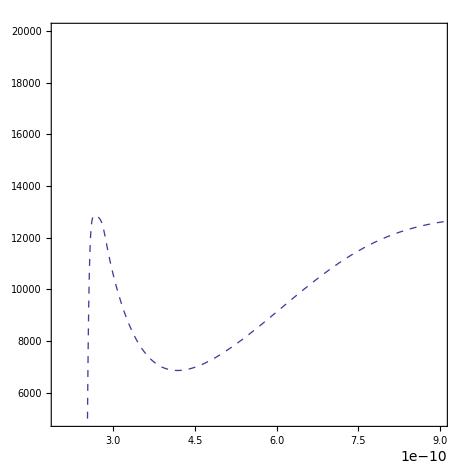

```mathematica
ppotA1SigmaPlus=Plot[A1SigmaPlusInt[x]+TeA1SigmaPlus-DeX,{x,2.4 10^-10,13 10^-10},AspectRatio->1,PlotRange->{{2. 10^-10,9. 10^-10},{5000,20000}},PlotStyle->Directive[Dashed,Thickness[0.002]]]
Plot[b3PiIntBox[x],{x,2.4 10^-10,12 10^-10},AspectRatio->1,PlotRange->{All,All}];
```

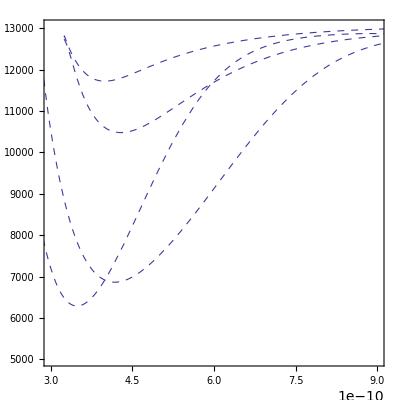

```mathematica
Show[ppotB1Pi,ppotc3SigmaPlus,ppotb3Pi,ppotA1SigmaPlus]
```

## Calculation of B1Π wavefunctions:

```mathematica
DisStep=10^-10/200; (* steps of 5 10^-13 m *)
EKin=-hbar^2/(2 muNa40K 1.6605 10^-27(DisStep )^2)/(c h)/100 (*kinetic energy in cm^(-1≥)*)
```

-46204.6

### Calculating Horizontal Profiles :

```mathematica
rstart=250;  (* start at 2.5 10^-10 m *)
rend=1500;  (* start at 15.0 10^-10 m *)
steps=Table[i,{i,2 rstart,2 rend}];
nsteps=Dimensions[steps][[1]];
```

```mathematica
DiagEntries=Table[-2EKin+B1PiIntBox[steps[[i]] DisStep ],{i,1,nsteps}];
RDiagEntries=Table[EKin,{i,1,nsteps-1}];
LDiagEntries=Table[EKin,{i,1,nsteps-1}];
B1PiHam=DiagonalMatrix[DiagEntries]+DiagonalMatrix[LDiagEntries,-1]+DiagonalMatrix[RDiagEntries,1];
```

InterpolatingFunction::dmval: Input value {1/4000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {501/2000000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {251/1000000000000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction will be suppressed during this calculation.

```mathematica
evalB1Pi=Reverse[Eigenvalues[B1PiHam]];
evecB1Pi=Reverse[Eigenvectors[B1PiHam]];
```

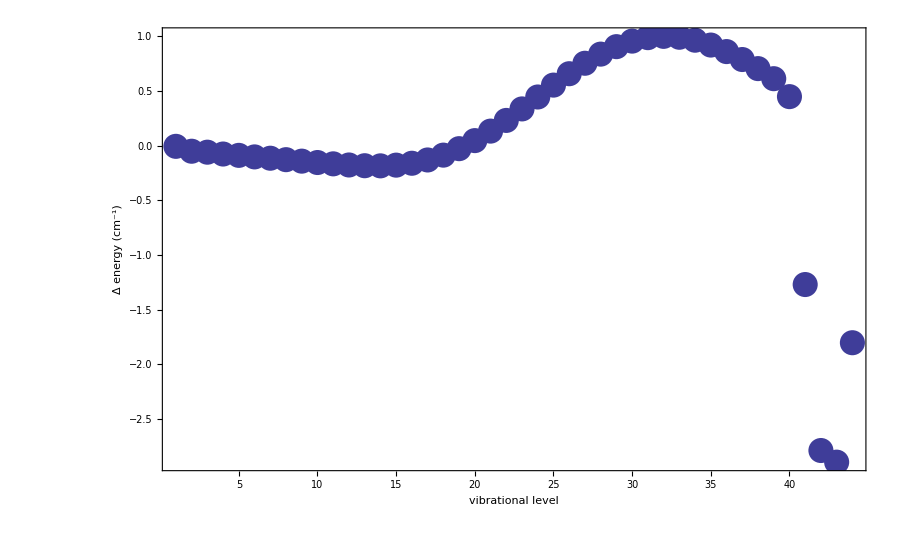

```mathematica
(* Here I check if the numerical eigenvalues coincide with the RKR eigenvalues... *)
ListPlot[(evalB1Pi-evalB1Pi[[1]]),PlotRange->{{0,50},{0,1500}},Frame->True,PlotStyle->PointSize[0.005]];
EnDiff=Table[evalB1Pi[[i]]-BoundstatesB1PiNa40K[[i,2]],{i,1,44}];
ListPlot[EnDiff,FrameLabel->{{"Δ energy (cm^-1)", },{"vibrational level","Deviation of vibrational energy from RKR (B1Π)"}},PlotRange->{0.1,-12}]
(* Seems quite good for the 30 vibrational levels *)
```

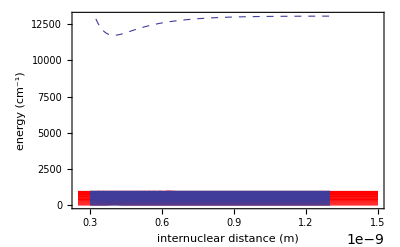

```mathematica
evecB1PiWF[i_]:=Table[{steps[[j]] DisStep ,3500 Abs[evecB1Pi[[i,j]]]^2+evalB1Pi[[i]]+ 0 TeB1Pi- 0DeX},{j,1,Dimensions[steps][[1]]}]
B1PiWFplots=Table[ListLinePlot[evecB1PiWF[i],PlotRange->All,Frame->True,AxesOrigin->{3 10^-10,1700},PlotStyle->Directive[Thickness[0.002],Red]],{i,1,20}];
RKRes=Table[Plot[BoundstatesB1PiNa40K[[v,2]]+0 TeB1Pi-0 DeX,{x,3 10^-10,13 10^-10}],{v,1,20}];
Show[B1PiWFplots,ppotB1Pi,RKRes,FrameLabel->{{"energy (cm^-1)", },{"internuclear distance (m)","Wavefunctions of B1Π potential"}}]
```

# Calculation of Wavefunctions for ground state potential X1Σ^+: (use Tiemann potential)

```mathematica
(*Definition of the parts of the parametrization*)
```

```mathematica
RepPart[R_,{A_,B_,q_}]:=A+B/R^q
InnerWellPart[R_,{b_,Rm_,alist_}]:=Sum[alist[[k]]((R-Rm)/(R+b Rm))^(k-1),{k,1,Dimensions[alist][[1]]}]
LongRangePart[R_,{Aex_,γ_,β_,Clist_}]:=-Clist[[1]]/R^6-Clist[[2]]/R^8-Clist[[3]]/R^10+Aex R^γ Exp[-β R]
```

```mathematica
(*Constants of the parametrization, energies in cm^-1, distances in 10^-10 m *)
```

```mathematica
(* repulsive part, smaller 2.53 x 10^-10 m *)
A=-0.44525554 10^4
B=0.107112840 10^6
q=8.3980
(* inner well part, larger 2.53 x 10^-10 m, smaller 11.3 x 10^-10 m *)
b=-0.4;
Rm=3.49901422 10^-10;
alist={-5273.6205,-0.1254 ,0.14536158×10^5 ,0.11484948×10^5 ,-0.3902171×10^3, -0.16931635×10^5 , -0.374520762×10^5,0.106906160×10^6, 0.5495867136×10^6,-0.2164021160×10^7, -0.10160808788×10^8, 0.22144308806×10^8, 0.10995928468×10^9,-0.15497420539×10^9,-0.782460886034×10^9,  0.764737283856×10^9, 0.3818679376129×10^10, -0.270560881733×10^10, -0.1307771478369×10^11,  0.6931241396136×10^10, 0.3179698977691×10^11 ,-0.1275832531699×10^11, -0.5474439830834×10^11, 0.1640384471424×10^11, 0.6534858404306×10^11, -0.139350481085×10^11,-0.5148927815627×10^11, 0.700666554236×10^10, 0.240949154116×10^11,-0.15757958492×10^10 ,-0.50725039078×10^10 };
(* long range part, larger 11.3 x 10^-10 m *)
Clist={0.1179302×10^8 10^-60,0.3023023×10^9 10^-80,0.9843378×10^10 10^-100};
γ=5.25669;
Aex=0.1627150×10^4 (10^-10)^γ;
β=2.11445 (1/10^-10);
```

-4452.56

107113.

8.398

```mathematica
(* constructing the complete potential: *)
```

```mathematica
lowcutgr=2.53 10^-10;
highcutgr=11.3 10^-10;
X1SigmaPot[R_]:=Piecewise[{{RepPart[R,{A,B,q}],R<lowcutgr},{InnerWellPart[R,{b,Rm,alist}],lowcutgr≤ R ≤highcutgr},{LongRangePart[R,{Aex,γ,β,Clist}],R>highcutgr}}]
```

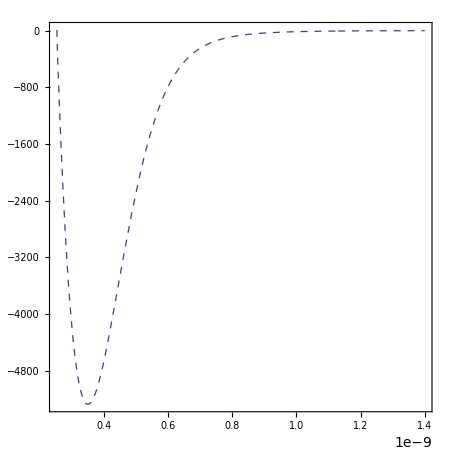

```mathematica
ppotX1sigma=Plot[X1SigmaPot[R],{R,lowcutgr,14 10^-10},AspectRatio->1,PlotRange->All,PlotStyle->Directive[Dashed,Thickness[0.002]]]
```

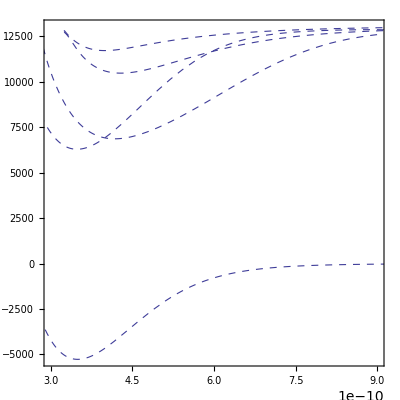

```mathematica
Show[ppotB1Pi,ppotc3SigmaPlus,ppotb3Pi,ppotA1SigmaPlus,ppotX1sigma]
```

### Calculating Horizontal Profiles :

```mathematica
DisStep=10^-10/200; (* steps of 5 10^-13 m *)
EKin=-hbar^2/(2 muNa40K 1.6605 10^-27(DisStep )^2)/(c h)/100 (*kinetic energy in cm^(-1≥)*);
```

```mathematica
steps=Table[i,{i,2 rstart,2 rend}];
nsteps=Dimensions[steps][[1]];
```

```mathematica
shift=5300; (*potential shift: just for convenience, producing nicer numbers *)
DiagEntries=Table[-2EKin+shift+X1SigmaPot[steps[[i]] DisStep ],{i,1,nsteps}];
RDiagEntries=Table[EKin,{i,1,nsteps-1}];
LDiagEntries=Table[EKin,{i,1,nsteps-1}];
X1SigmaHam=DiagonalMatrix[DiagEntries]+DiagonalMatrix[LDiagEntries,-1]+DiagonalMatrix[RDiagEntries,1];
```

```mathematica
evalX1Sigma=Reverse[Eigenvalues[X1SigmaHam]];
evecX1Sigma=Reverse[Eigenvectors[X1SigmaHam]];
```

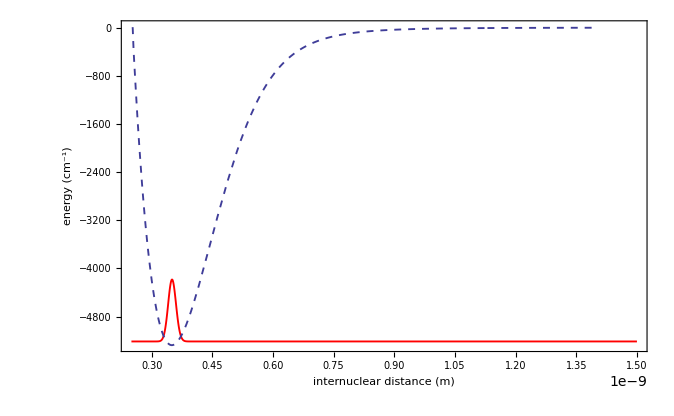

```mathematica
evecX1SigmaWF[i_]:=Table[{steps[[j]] DisStep ,50000 Abs[evecX1Sigma[[i,j]]]^2+evalX1Sigma[[i]]-shift},{j,1,Dimensions[steps][[1]]}]
X1SigmaWFplots=Table[ListLinePlot[evecX1SigmaWF[i],PlotRange->All,Frame->True,AxesOrigin->{3 10^-10,0},PlotStyle->Directive[Thickness[0.002],Red]],{i,1,1}];
Show[X1SigmaWFplots,ppotX1sigma,FrameLabel->{{"energy (cm^-1)", },{"internuclear distance (m)","Wavefunctions of X1Σ^+ potential"}}]
```

### Ground (X1Σ^+) and excited (B1Π) state potential and wavefunctions:

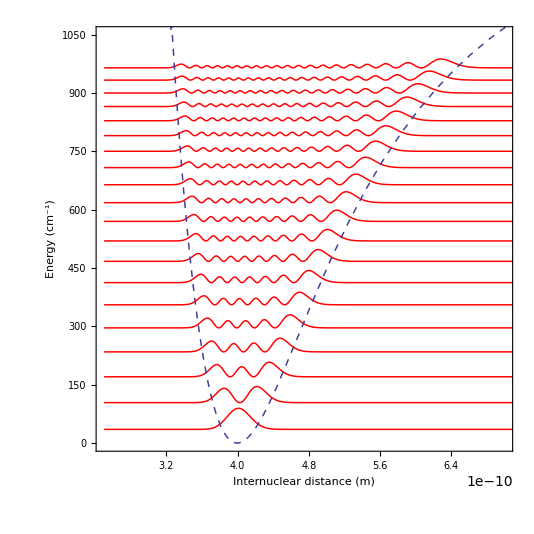

```mathematica
Show[B1PiWFplots,ppotB1Pi,FrameLabel->{{"Energy (cm^-1)", },{"Internuclear distance (m)","Wavefunctions of B1Π potential"}},PlotRange->{{2.5 10^-10,7 10^-10},{0,1050}}, AxesOrigin->{0,0},AspectRatio->1]
```

### Calculate Frank - Condon Factors :

```mathematica
(* Normalizing wavefunctions *)
```

```mathematica
NWF[wf_,step_]:=Module[{nconst},
nconst=Total[step wf^2];
wf/Sqrt[nconst]
]
```

```mathematica
NevecB1Pi=Table[NWF[Chop[evecB1Pi[[i]]],DisStep],{i,1,Dimensions[evecB1Pi][[1]]}]
```

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,«2229»,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},«2499»,{«22»,«2499»,0}}

```mathematica
NevecX1Sigma=Table[NWF[Chop[evecX1Sigma[[i]]],DisStep],{i,1,Dimensions[evecX1Sigma][[1]]}];
```

```mathematica
Total[DisStep NevecX1Sigma[[1]]^2]
```

1.

#### Frank - Condon factors :

```mathematica
(* Note: Both wavefunctions must be discretized on the same grid! Furthermore WF should be normalized! *)
```

```mathematica
FC[wf1_,wf2_]:=Module[{},
Sum[(steps [[i]]DisStep)^2 wf1[[i]]wf2[[i]],{i,1,Dimensions[steps][[1]]}]^2
]
```

```mathematica
NevecX1Sigma[[1]];
```

```mathematica
FCgroundstatewithB1Pi=Table[{i,10^14 FC[NevecX1Sigma[[1]],NevecB1Pi[[i+1]]]},{i,0,20}]
ListPlot[FCgroundstatewithB1Pi,FrameLabel->{{"Frank-Condon factor (a.u.)", },{"internuclear distance (m)","Frank-Condon of B1Pi with "}},PlotRange->{{ 0,20},{0.,10^(=14)}},AspectRatio->1]
```

{{0,4.2015×10^-16},{1,1.69193×10^-15},{2,3.67056×10^-15},{3,5.70752×10^-15},{4,7.1493×10^-15},{5,7.68614×10^-15},{6,7.38035×10^-15},{7,6.50473×10^-15},{8,5.36615×10^-15},{9,4.20616×10^-15},{10,3.16925×10^-15},{11,2.31673×10^-15},{12,1.65548×10^-15},{13,1.16363×10^-15},{14,8.08747×10^-16},{15,5.58276×10^-16},{16,3.84248×10^-16},{17,2.64585×10^-16},{18,1.82802×10^-16},{19,1.27045×10^-16},{20,8.90107×10^-17}}

{{0,0.0042015},{1,0.0169193},{2,0.0367056},{3,0.0570752},{4,0.071493},{5,0.0768614},{6,0.0738035},{7,0.0650473},{8,0.0536615},{9,0.0420616},{10,0.0316925},{11,0.0231673},{12,0.0165548},{13,0.0116363},{14,0.00808747},{15,0.00558276},{16,0.00384248},{17,0.00264585},{18,0.00182802},{19,0.00127045},{20,0.000890107}}

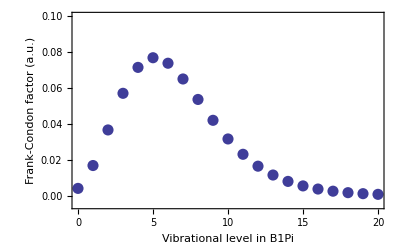

```mathematica
FCgroundstatewithB1Pi=Table[{i,10^13 FC[NevecX1Sigma[[1]],NevecB1Pi[[i+1]]]},{i,0,20}]
ListPlot[FCgroundstatewithB1Pi,PlotRange->{-0.005,0.1},FrameLabel->{{"Frank-Condon factor (a.u.)", },{"Vibrational level in B1Pi",}}]
```